# Quantum Mechanics

## Part I. State and Operator

## Quantum States

### Ket and Bra

#### State as a Vector

Quantum mechanics is a physics theory that describes the behavior of quantum systems (microscopic particles, strings, qubits ...).

What does physics theory do in general?

Describe the state of the system: a set of variables encoding the relevant information of the system.

Predict (i) the observables (measurement outcomes) and (ii) their dynamics (time evolution).

Physics theory is about encoding the physical reality in the form of information and generating predictions about the reality based on such information.

State variables are inferred from observations.

State variables may not have “physical meaning”.

Choice of state variables may not be unique. (There can be more than one way to describe a system.)

Example: how to describe the following images?

```mathematica
Block[{dat},
dat=ColorNegate/@RandomChoice[#,3]&/@GroupBy[ResourceData["MNIST","TestData"],Last->First];Grid[Partition[RandomSample@Flatten@Values@dat,6]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Image file: brightness of each pixel. - describe a state by all possible observables.

Human: digits 0, 1, 2, …, 9. - describe a state by a name.

Machine learning: feature vectors in the latent space. - describe a state by a vector in a vector space. [This is the most close to what we do in quantum mechanics.]

```mathematica
Block[{dat,imgs,pts},
dat=ColorNegate/@RandomChoice[#,3]&/@GroupBy[ResourceData["MNIST","TestData"],Last->First];
imgs=Flatten@Values@dat;
SeedRandom[449];
pts=Flatten[Table[#+ϵ,{ϵ,0.2RandomVariate[NormalDistribution[],{3,2}]}]&/@RandomVariate[NormalDistribution[],{10,2}],1];
pts=pts/Max[Norm/@pts];
Graphics[{{Arrow[{#,0}&/@{-1,1.2}],Text["feature 1",{1.2,0},{1,1}],Arrow[{0,#}&/@{-1,1.2}],Text["feature 2",{0,1.2},{1,-1},{0,1}]},Inset[#1,#2,{0,0},0.15]&@@@Thread[{imgs,pts}]},PlotRange->All,ImageSize->180]]
```

-Graphics-

In quantum mechanics, every state of a quantum system is described by a complex vector (an array of complex numbers).

The vector components are the state variables, and they may not need to have physical meanings. [They are also called probability amplitudes or wave amplitudes, but I don’t explain what is “waving” here.]

This particular (vector-based) approach of describing quantum states is not the only way. There are other ways to formulate quantum mechanics, just to name a few: density matrix formulation (matrix-based), classical shadow formulation (probability-based) [Reference], quantum bootstrap (observable-based) [Reference].

However, the vector description is a simple and efficient way to describe a (pure) state of a quantum system. So we will start from state vectors.

Information encoded in a quantum state is called quantum information. It provides the foundation for quantum computation/communication.

Hsin-Yuan Huang, Richard Kueng, John Preskill. arXiv:2002.08953.

Xizhi Han, Sean A. Hartnoll, Jorrit Kruthoff. arXiv:2004.10212.

Example: a (quantum) traffic light system.

One-hot Encoding: A traffic light system has three distinct states: red, yellow and green. In quantum mechanics, they can be described by three orthogonal one-hot vectors:

```mathematica
Block[{state},
state[y0_]:=Graphics[{{Black,Rectangle[{0,0},{1,3},RoundingRadius->0.5]},Table[{Darker[<|1->Green,2->Yellow,3->Red|>[y],0.7-0.7Boole[y+y0==4]],Disk[{0.5,y-0.5},0.4]},{y,3}]},ImageSize->15];
Style[Column[Table[Row[{Ket[state[s]]," = ",MatrixForm[SparseArray[{s,1}->1,{3,1}]]}],{s,3}]],14,FontFamily->"CMU"]]
```

-Graphics- = (1
0
0)
-Graphics- = (0
1
0)
-Graphics- = (0
0
1)

Distinct states. Two states are distinct, if they can be be distinguished by the different observation values of an observable.

Quantum superposition. What is peculiar about quantum states is that quantum mechanics allows us to write down linear combinations of states, which has no classical correspondence.

1/(√6)(1
ⅈ
-2)=1/(√6)(+ⅈ-2).

Mathematically this is ok, but physically what does it mean?

Well, the norm square of the superposition coefficients has the statistical interpretation of probability.

state | coeffient | probability
 | 1/(√6) | (|1/(√6)|)^2=1/6
 | ⅈ/(√6) | (|ⅈ/(√6)|)^2=1/6
 | -2/(√6) | (|-2/(√6)|)^2=2/3

The traffic light has 1/6 of the probability to be observed in red, and 1/6 in to be in yellow, and 2/3 to be in green.

But what about the relative sign or phase of the superposition coefficients? - The complex nature of the state vector component is a feature that enables quantum interference.

To better understand the meaning of the state vector, we need to understand how quantum mechanics predicts observables from the state. This is the only way decode the quantum information back to the physical reality.

#### Ket Vector

Postulate 1 (States): States of a quantum system are described as (rays of) vectors in the associated Hilbert space.

In Dirac’s notation, a quantum state will be denoted by a ket (or ket state, ket vector) v, which is an element in a complex vector space ℋ

v∈ℋ.

Vector space. The defining property of a vector space is that linear combinations of vectors are still in the vector space

∀u,v∈ℋ;α,β∈ℂ:
αu+βv∈ℋ.

The fact that ℋ is a complex vector space is reflected in the fact that α and  β are complex numbers.

This can be generalized to many vectors: any linear combinations of vectors is still a vector

∀{u_n}⊂ℋ;{α_n}⊂ℂ:
∑_n α_n u_n∈ℋ.

Superposition Principle: any linear combination of quantum states of a given quantum system is still a valid quantum state of the same system.

Vector representation: Each ket can be represented as a column vector

v≏(v_1
v_2
⋮).

Note: “≏” implies the vector representation is basis dependent and the values of vector components may change if we view the same state in a different basis.

If v≏(v_1
v_2), w≏(w_1
w_2), what is the vector representation of the state v+w and λv (λ∈ℂ is a complex scalar).

Addition: each component adds up separately

v+w≏(v_1
v_2)+(w_1
w_2)=(v_1+w_1
v_2+w_2).

Scalar multiplication: distribute the scalar factor to each component and multiply separately

λv≏λ(v_1
v_2)=(λ v_1
λ v_2)

To write down the vector representation, we must specified a set of (orthonormal) basis vectors in the vector space ℋ, and represent them as one-hot unit vectors:

1≏(1
0
⋮),2≏(0
1
⋮), ….

Such that v can be expressed as a linear combination of basis vectors

v=v_1 1+v_2 2+…
=∑_i v_i i.

The ith vector component v_i is the linear combination coefficient in front of the ith basis vector i.

Example: a qubit system.

A qubit (or quantum-bit) is a quantum system that has two distinct states.

The two distinct states are 0 and 1.

We can choose 0 and 1 to be the basis vectors (like choosing a coordinate system) and write:

0≏(1
0), 1≏(0
1)

The vector representation of a quantum state is also called a state vector.

By saying that a qubit is a two-state system, its state vector has two components.

A generic quantum state of a qubit is a complex linear superposition of the basis states

ψ=ψ_0 0+ψ_1 1≏(ψ_0
ψ_1).

ψ_0,ψ_1∈ℂ are complex numbers. They parameterize the state ψ.

Conversely, every two-component complex vector describes a qubit state.

Statistical interpretation: (|ψ_0|)^2 and (|ψ_1|)^2 are respectively the probabilities to observe the qubit in the 0 and the 1 states.

Define the following qubit states: 
+=1/(√2)(0+1), 
-=1/(√2)(0-1), 
ⅈ=1/(√2)(0+ⅈ1). 
Express the state ⅈ as a quantum superposition of states + and - (i.e. find the linear combination coefficients).

#### Bra Vector (I)

In Dirac’s notation, a bra u is a dual vector of a ket u. The name comes from the fact that they combine into a bracket, which represents a scalar product [to be introduced later].

If u is a linear combination of v and w

u=αv+βw,

then its dual is

u=α^*v+β^*w.

Under duality: (i) ket is flipped to bra (and vice versa), (ii) every scalar coefficient gets complex conjugated.

Vector representation: Each bra can be represented as a row vector. If the ket vector (column vector) is

v≏(v_1
v_2
⋮),

then the bra vector (dual row vector) is simply the conjugate transpose of the ket vector

v≏(v_1^* | v_2^* | ⋯).

Every basis vector i also has a dual basis vector i, the are represented as

1≏(1 | 0 | ⋯),
2≏(0 | 1 | ⋯),
⋯.

The dual basis vectors form a set of basis for the bra vector. In terms of basis vectors,

v=v_1^*1+v_2^*2+…
=∑_i v_i^*i.

The ith vector component v_i^* is the linear combination coefficient in front of the ith dual basis vector i.

#### Scalar Product

Scalar product (or inner product) is a function that takes two vectors, u and v, and returns a complex number, denoted as uv.

·· | : | ℋ×ℋ | → | ℂ
  |   | u,v | ↦ | uv

It must satisfy the following defining properties:

Complex conjugation

∀u,v∈ℋ, uv=vu^*

Note: uv≠vu in general, unless uv∈ℝ.

Linearity of the ket vector

∀u,v,w∈ℋ;α,β∈ℂ:
u(αv+βw)=αuv+βuw.

(Anti)linearity of the bra vector: using Eq. (DisplayFormulaNumbered), Eq. (DisplayFormulaNumbered), one can show

(α^*v+β^*w)u=α^*vu+β^*wu.

Note: we follow the convention in Eq. (DisplayFormulaNumbered) to denote the linear combination of bra vectors, which is different from the textbook notation (2.23).

Show that Eq. (DisplayFormulaNumbered) is implied by Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Take a complex conjugation on both sides of Eq. (DisplayFormulaNumbered)

(α^*v+β^*w)u
=[u(αv+βw)]^*
=(αuv+βuw)^*
=α^*uv^*+β^*uw^*
=α^*vu+β^*wu.

Scalar product of any vector v with itself is real and positive definite,

vv>=0.

More specifically,

vvPiecewise[{{=0, if v=0}, {>0, otherwise}}].

This implies the Cauchy-Schwarz inequality

(|uv|)^2<=uuvv.

Prove Eq. (DisplayFormulaNumbered).

(i) Trivial case: when v=0 is a zero vector,

uv= vv=0,

Eq. (DisplayFormulaNumbered) trivially holds as an equality.

(ii) Non-trivial case: when v≠0, i.e.  vv>0. Let

w=uvv-vvu,

one can show that

ww=(vvu-uvv)(uvv-vvu)
=vvuuvv-vvuvvu-uvvuvv+uvvvvu
=vv(uuvv-uvvu).

Given that vv>0, we have

uuvv-uvvu=ww/vv>=0,

as ww≥0 following from Eq. (DisplayFormulaNumbered). This proves the inequality Eq. (DisplayFormulaNumbered), as

(|uv|)^2=uvvu≤uuvv.

In the vector representation (assuming an orthonormal basis), take two states

v≏(v_1
v_2
⋮), w≏(w_1
w_2
⋮),

the scalar product can be taken as

vw≏(v_1^* | v_2^* | ⋯)(w_1
w_2
⋮)
=v_1^*w_1+v_2^*w_2+…
=∑_i v_i^*w_i.

Verify that Eq. (DisplayFormulaNumbered) is consistent with the defining properties of the scalar product in Eq. (DisplayFormulaNumbered), Eq. (DisplayFormulaNumbered), Eq. (DisplayFormulaNumbered).

Check Eq. (DisplayFormulaNumbered):

uv=∑_i u_i^*v_i
=∑_i (u_i v_i^*)^*
=(∑_i v_i^*u_i)^*
=vu^*.

Check Eq. (DisplayFormulaNumbered):

u(αv+βw)
=∑_i u_i^*(α v_i+β w_i)
=∑_i (α u_i^*v_i+β u_i^*w_i)
=α∑_i u_i^*v_i+β∑_i u_i^*w_i
=αuv+βuw.

Check Eq. (DisplayFormulaNumbered):

(α^*u+β^*v)w
=∑_i (α u_i+β v_i)^*w_i
=∑_i (α^* u_i^*w_i+β^* v_i^*w_i)
=α^* ∑_i u_i^*w_i+β^*∑_i v_i^*w_i
=α^*uw+β^*vw.

Hilbert space: a vector space equipped with a scalar product.

Every quantum system is associated with a Hilbert space. Its different quantum states are different vectors in the same Hilbert space.

#### Bra Vector (II)

Linear functional Φ on a vector space ℋ is a linear map that associates each vector in ℋ with a complex number.

Φ | : | ℋ | → | ℂ
  |   | v | ↦ | Φ(v)=z

Linearity requires Φ to satisfy

∀v,w∈ℋ;α,β∈ℂ:
Φ(αv+βw)=α Φ(v)+β Φ(w)

Example: “take the first component” functional

Let Φ_1 be a function that maps any vector v to its first component v_1

Φ_1(v)=v_1.

This is a linear functional on the vector space.

Φ_1(αv+βw)=α v_1+β w_1=α Φ_1(v)+β Φ_1(w).

Denote the first basis vector as 1, Φ_1 can be written as the scalar product:

Φ_1(v)=1v.

In general, every ket vector u defines a corresponding linear functional through the scalar product:

Φ_u(v)=uv.

Conversely, in mathematics, this corresponding linear functional is treated as the definition of the dual bra vector u=Φ_u of the original ket vector u.

Riesz theorem: any bounded linear functional acting on a Hilbert space ℋ can be represented as a scalar product of the form in Eq. (DisplayFormulaNumbered).

Dual vector space. The space of such functionals (bra vectors) is  called the dual vector space of ℋ, denoted as ℋ^*. The dual vector space ℋ^* is the space of bra vectors.

### Norm and Orthogonality

#### Norm

Squared norm of a vector v is the scalar product of the vector with itself, denoted as

(‖v‖)^2=vv.

Taking off the square, ‖v‖=√vv is the norm of v.

Normalized state: a state v is normalized ⇔ Its norm is one, i.e.

(‖v‖)^2=vv=1.

Example: Consider a qubit state

v≏(v_0
v_1),

the normalization condition means

vv=v_0^*v_0+v_1^*v_1=1.

In general, the normalization condition means

vv=∑_i (|iv|)^2=∑_i (|v_i|)^2=1.

According to the statistical interpretation of quantum state, (|v_i|)^2 is the probability to observe the system in the ith basis state. The normalization condition is simply a requirement that the probabilities must sum up to unity.

Normalization of a state: if a state v was not normalized, it can be normalized by

v->v/(‖v‖)=1/(√vv)v,

unless ‖v‖ is zero or infinity.

Normalize the vector v≏(1
2ⅈ).

Step 1: calculate the norm

vv=(1 | -2ⅈ)(1
2ⅈ)=1+4=5.
√vv=√5.

Step 2: divide the vector by the norm

v->1/(√vv)v
≏1/(√5)(1
2ⅈ).

#### Orthogonality

Orthogonal states: two states u and v are orthogonal to each other ⇔ their scalar product is zero, i.e.

uv⟩=0.

For example, the qubit states |0⟩ and |1⟩ (see Eq. (DisplayFormulaNumbered)) are orthogonal, as

01=(1 | 0)(0
1)=0.

|0⟩ and |1⟩ are orthogonal for a good reason: they are distinct states of a qubit, i.e. if the qubit is in state 0, it is definitely not in state 1, vice versa.

Orthogonal subspaces: two subspaces ℋ_1 and ℋ_2 in ℋ are orthogonal if

∀u∈ℋ_1,v∈ℋ_2: uv⟩=0.

Complementary subspace: ℋ_(1,⊥) is the complementary subspace of ℋ_1, if ℋ_1 and ℋ_(1,⊥) are orthogonal and ℋ_1⊕ℋ_(1,⊥)=ℋ.

For each v∈ℋ, there is a unique decomposition:

v=v_∥+v_⊥,

such that v_∥∈ℋ_1 and v_⊥∈ℋ_(1,⊥).

v_∥ is the projection of v in ℋ_1.

Consider a Hilbert space ℋ spanned by three vectors 
x≏(1
0
0), y≏(0
1
0), z≏(0
0
1). 
(i) Let ℋ_∥=span{x,y} and ℋ_⊥=span{z}. Show that ℋ_∥ and ℋ_⊥ are orthogonal subspaces.
(ii) For v=v_x x+v_y y+v_z z, find the unique decomposition v=v_∥+v_⊥, such that v_∥∈ℋ_∥ and v_⊥∈ℋ_⊥.

(i) Because ℋ_∥ is spanned by x and y, for any u∈ℋ_∥, u must be a linear combination of x and y, i.e.

u=u_x x+u_y y.

For the same reason, because ℋ_⊥=span{z}, any w∈ℋ_∥ must take the form of

w=w_z z.

Given the fact that xz=yz=0, we can show

uw=(u_x^*x+u_y^*y)w_z z
=u_x^*w_z xz+u_y^*w_z yz
=0+0=0,

which holds for all u∈ℋ_∥ and w∈ℋ_∥. Therefore by definition Eq. (DisplayFormulaNumbered), ℋ_∥ and ℋ_⊥ are orthogonal subspaces.

(ii) To find v_∥∈ℋ_∥ and v_⊥∈ℋ_⊥, assume there exist some coefficients v_(1,2,3)∈ℂ that

v_∥=v_1 x+v_2 y,
v_⊥=v_3 z.

If the decomposition v=v_∥+v_⊥ exists, it would imply

v=v_∥+v_⊥=v_1 x+v_2 y+v_3 z.

On the other hand,

v=v_x x+v_y y+v_z z.

By comparing Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we uniquely determine

v_1=v_x, v_2=v_y, v_3=v_z.

So there exist the unique decomposition of any v∈ℋ in the orthogonal subspaces ℋ_∥ and ℋ_⊥, given by

v_∥=v_x x+v_y y,
v_⊥=v_z z.

Therefore ℋ_∥⊕ℋ_⊥=ℋ, i.e. ℋ_∥ and ℋ_⊥ are complementary subspaces.

#### Ray and Phase Ambiguity

If v and v' are related by a scalar multiplication (for λ∈ℂ)

v'=λv,

they describe the identical physical state of the quantum system. A picture in the real vector space would be like: (the vectors on a ray are all equivalent)

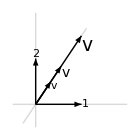

```mathematica
Block[{θ=5π/16},
Graphics[{{AbsoluteThickness[1],LightGray,Line[{-0.5#,2#}&/@{{1,0},{0,1},{Cos[θ],Sin[θ]}}]},Arrowheads[0.05],{Arrow[{{0,0},#1}],Text[#2,#1,#3]}&@@@{{{1,0},"\!\(1\)",{-1,0}},{{0,1},"\!\(2\)",{0,-0.5}}},
{Arrow[{{0,0},#1{Cos[θ],Sin[θ]}}],Text[Style["\!\(v\)",14 Sqrt[#1]],#1{Cos[θ],Sin[θ]},{-1,1}]}&@@@{{0.6},{1},{1.8}}},ImageSize->140]]
```

Precisely speaking, quantum states are described by rays of vectors in the Hilbert space, i.e. only the “direction” of state vector matters.

The square norm of the state vector does not affect the physical property of the quantum system, because it represent the total probability of observation outcomes, which can always be taken to 1.

To fix the norm ambiguity, we will always require a state vector to be normalized, i.e. vv=1.

The overall phase of the state vector also does not matter, as it turns out that all physical properties about the quantum system is always unchanged under v→ⅇ^(ⅈ φ)v.

But there is no canonical way to fix the phase ambiguity. We must ensure that any prediction about the quantum system must not rely on the overall phase on the formulation level.

#### Fidelity

The fidelity F(u,v) between two quantum states u and v quantifies the similarity (overlap) between two states. It is given by the squared absolute value of their scalar product (assuming the normalization of state vectors)

F(u,v)=(|uv|)^2.

Fidelity is symmetric: F(u,v)=F(v,u).

Fidelity takes values in the range of

0<=F(u,v)≤1.

This follows from the Cauchy-Schwarz inequality of scalar product Eq. (DisplayFormulaNumbered) that (|uv|)^2<=uuvv.

Statistical interpretation: If a quantum system is known to be in a state v, observing the system again may find the system in another state u with probability

p(u|v)=(|uv|)^2.

Detailed balance: the probability to observe one state on another is the same as the other way round

p(u|v)=p(v|u)=F(u,v)=(|uv|)^2.

Identical states. Two states u and v are identical iff the fidelity between them is one (fully overlap)

(|uv|)^2=1.

This is only achievable when

u=ⅇ^(ⅈ φ)v,

i.e. the two states are the same up to phase ambiguity.

Reality must be confirmable by repeated observations: if a quantum system is known to be in a state v, observing the system again will certainly confirm the state v (with probability 1).

Distinct states. Two states u and v are distinct iff the fidelity between them is zero (no overlap)

(|uv|)^2=0.

Orthogonal states ⇔ distinct realities.

Distinct realities are distinguishable by repeated observations: if a quantum system is known to be in a state v, observing the system again will certainly not find the system in another orthogonal state u.

Overlapping states. In general, two different states u and v may have partial overlap (they don’t need to be orthogonal), i.e. their fidelity falls between zero and one

0<(|uv|)^2<1.

Realities can overlap: if two quantum states are more similar to (more overlapped with) each other, the probability to confuse them is higher.

3≏-Graphics-, 5≏-Graphics-.

Therefore, there is generally some probability to observe one state given another state, if the two states has some similarity.

### Basis

#### General Basis

A set of vectors {e_i:i=1,2...} are said to be linearly independent, if

∑_i c_i e_i=0⇔∀i:c_i=0,

i.e. none of the vectors in the set can be written as a linear combination of the others.

Basis: a basis ℬ of a vector space ℋ is a set of linearly independent vectors ℬ={e_i:i=1,2...} that span the full space of ℋ, denoted as

ℋ=span ℬ,

i.e. any vector in ℋ can be expanded as a linear combination of the basis vectors

∀v∈ℋ,∃{v_i}⊂ℂ:v=∑_i v_i e_i.

The coefficients v_i depend on what vector v is being expanded.

The dimension of the vector space dim ℋ = the number of basis vectors = the maximal number of linearly independent vectors in the space.

The Hilbert space dimension of a quantum system can be finite or infinite. Example: a qubit - dim ℋ=2, ten qubits - dim ℋ=2^10=1024, a particle in a continuous space - dim ℋ=∞.

The summation in Eq. (DisplayFormulaNumbered) becomes a infinite sum (countable) or an integration (uncountable) when the Hilbert space dimension is infinite.

Dimension of the Hilbert space is often a choice: we don’t really know how many independent states are there in a quantum system. We only care about the states that are relevant to us.

#### Orthonormal Basis

Orthonormal basis: a basis ℬ={i:i=1,2,…} in which the basis vectors are normalized and orthogonal to each other.

ij=δ_ij=Piecewise[{{1, i=j,}, {0, i≠j.}}]

Each orthogonal basis state describes a distinct reality of the quantum system.

Example: 0 and 1 form an orthonormal basis of the qubit Hilbert space. They represent two distinct realities: if the qubit is in state 0, it is definitely not in state 1 (and vice versa).

Completeness: Any full set of distinct states in the Hilbert space ℋ forms a complete set of orthonormal basis ℬ, such that every state v∈ℋ can be expanded as a linear superposition of the basis states,

v=v_1 1+v_2 2+…=∑_(i∈ℬ) v_i i.

The superposition coefficient v_i are the components of the state vector, which can be extracted by the scalar product with the basis state,

v_i=iv.

Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) can be written in a more elegant form in terms of bras and kets only

v=∑_(i∈ℬ) iiv.

The squared norm of a state v is the sum of squared norm of its components on (any) orthonormal basis.

vv=∑_i (|iv|)^2=∑_i (|v_i|)^2.

Using the orthonormal property ij=δ_ij to evaluate the norm of v=∑_i iiv.

(‖v‖)^2=vv
=(∑_j vjj)(∑_i iiv)
=∑_(i,j) vjijiv
=∑_(i,j) vj δ_ij iv
=∑_i viiv
=∑_i v_i^*v_i
=∑_i (|v_i|)^2.

Orthonormal basis states are represented by one-hot vectors, as they are normalized and orthogonal to each other

1≏(1
0
0
⋮), 2≏(0
1
0
⋮), 3≏(0
0
1
⋮), ….

Choosing a basis is always a helpful practice in quantum mechanics. But quantum mechanics can be formulated in a basis independent manner.

Let {0,1} be an orthonormal basis of a qubit, consider the following linear combinations 
0'=e^(ⅈ φ/2)cos(θ/2)0+e^(-ⅈ φ/2)sin(θ/2)1,
1'=-e^(ⅈ φ/2)sin(θ/2)0+e^(-ⅈ φ/2)cos(θ/2)1, 
where θ and φ are arbitrary real angles. Show that 0' and 1' also form an orthonormal basis (for any choices of  θ and φ).

### Summary

States are vectors.

Ket and bra:

| ket | bra (dual)
Hilbert space | ℋ | ℋ^*
basis | ℬ={i} | ℬ^*={i}
state | v=∑_i v_i i | v=∑_i v_i^*i
vector | (v_1
v_2
⋮) | (v_1^* | v_2^* | ⋯)
component | v_i=iv | v_i^*=vi

Scalar product

uv=∑_i uiiv=∑_i u_i^*v_i.

Normalized state vv=1. To normalize a state:

v→v/(√vv).

Orthogonal states uv=0.

Orthonormal basis ℬ={i:ij=δ_ij}.

Fidelity (similarity between quantum states)

F(u,v)=(|uv|)^2 Piecewise[{{=1, identical states}, {=0, distinct states}, {∈(0,1), overlapping states}}].

Statistical interpretation: p(u|v)=p(v|u)=F(u,v).

## Quantum Operators

### Operator and Matrix

#### Operator

Operator: an operator acts on a state and returns a new state.

Ô | : | ℋ | → | ℋ
  |   | v | ↦ | w=Ô v

Distinction: operator is a vector-to-vector mapping, while functional is a vector-to-scalar mapping.

Linear operator: an operator Ô is say to be linear if it satisfies the linear property

∀u,v∈ℋ;α,β∈ℂ:
Ô(αu+βv)=α Ô u+β Ô v.

In quantum mechanics, all operators are linear operators (we will omit the adjective “linear” from now on).

Identity operator is a special operator that maps any state to itself (the do-nothing operator), denoted as 𝟙.

∀v: 𝟙v=v.

#### Operator as a Matrix

Given an orthonormal basis  ℬ={i:i=1,2,…} of the Hilbert space ℋ, every operator acting on ℋ can be expanded as a linear combination of basis operators ij,

Ô=∑_(i,j) i O_(i,j)j,

O_(i,j)∈ℂ are complex coefficients, which can be extracted by

O_(i,j)=i Ô j.

Prove Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

i Ô j=i(∑_(k,l) k O_(k,l)l)j
=∑_(k,l) ik O_(k,l)lj
=∑_(k,l) δ_(i,k)O_(k,l)δ_(l,j)
=O_(i,j).

ij denotes the operator that take the system from state j to state i, because

(ij)k=ijk=i δ_(j,k)
=Piecewise[{{i, if k=j,}, {0, if k≠j.}}]

Matrix representation. Every operator can be represented as a matrix

Ô≏(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱).

The ith row jth column matrix element O_(i,j) is the linear combination coefficient in front of the basis operator ij.

Use the vector representation of ket and bra basis to show Eq. (DisplayFormulaNumbered) is the corresponding representation of  Eq. (DisplayFormulaNumbered).

Ô=∑_(i,j) i O_(i,j)j
=1 O_(1,1)1+1 O_(1,2)2+2 O_(2,1)1+2 O_22 2+…
=(1
0
⋮)O_(1,1)(1 | 0 | ⋯)+(1
0
⋮)O_(1,2)(0 | 1 | ⋯)+(0
1
⋮)O_(2,1)(1 | 0 | ⋯)+(0
1
⋮)O_(2,2)(0 | 1 | ⋯)+…
=O_(1,1)(1 | 0 | ⋯
0 | 0 | ⋯
⋮ | ⋮ | ⋱)+O_(1,2)(0 | 1 | ⋯
0 | 0 | ⋯
⋮ | ⋮ | ⋱)+O_(2,1)(0 | 0 | ⋯
1 | 0 | ⋯
⋮ | ⋮ | ⋱)+O_(2,2)(0 | 0 | ⋯
0 | 1 | ⋯
⋮ | ⋮ | ⋱)+…
=(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱).

Example: Identity operator

Identity operator is universally represented by the identity matrix in any orthonormal basis (independent of the basis choice).

According to Eq. (DisplayFormulaNumbered),

𝟙_ij=i𝟙j=ij=δ_ij=Piecewise[{{1, i=j}, {0, i≠j}}].

In matrix representation Eq. (DisplayFormulaNumbered),

𝟙=(1 |   |  
  | 1 |  
  |   | ⋱).

Using Dirac notation Eq. (DisplayFormulaNumbered),

𝟙=∑_(i,j) i 𝟙_ij j=∑_(i,) ii.

This is also call the resolution of identity.

Example: Pauli operators

Pauli operators are a set of operators acting on a qubit.

(σ̂)^x=10+01,
(σ̂)^y=ⅈ 10-ⅈ01,
(σ̂)^z=00-11,

Sometimes the identity operator

𝟙=00+11,

is also included as the 0th Pauli operator.

Pauli matrices - matrix representations of Pauli operators on the qubit basis {0,1}:

𝟙≏(1 | 0
0 | 1),(σ̂)^x≏(0 | 1
1 | 0), (σ̂)^y≏(0 | -ⅈ
ⅈ | 0), (σ̂)^z≏(1 | 0
0 | -1).

#### Operator Acting on State

Applying an operator to a state ≏ multiplying a matrix to a vector.

Consider an operator Ô acting on a state v resulting in a state w

w=Ô v,

where states and operators are expanded as

v=∑_i v_i i, w=∑_i w_i i,
 Ô=∑_(i,j) i O_(i,j)j.

The expansion coefficients are related by the matrix-vector multiplication

w | = | Ô | v
↓^≏ |   | ↓^≏ | ↓^≏
(w_1
w_2
⋮) | = | (O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱) | (v_1
v_2
⋮)

or equivalently

w_i=∑_j O_(i,j)v_j.

Prove the statement Eq. (DisplayFormulaNumbered) using Eq. (DisplayFormulaNumbered).

Starting from w=Ô v, the right-hand-side:

Ô v=(∑_(i,j) i O_(i,j)j)(∑_k v_k k)
=∑_(i,j,k) O_(i,j)v_k ijk
=∑_(i,j,k) O_(i,j)v_k i δ_(j,k)
=∑_(i,j) O_(i,j)v_j i
=∑_i (∑_j O_(i,j)v_j)i,

while the left-hand-side:

w=∑_i w_i i.

To identify them, we must have

w_i=∑_j O_(i,j)v_j,

which is the definition of matrix-vector multiplication

(w_1
w_2
⋮)=(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)(v_1
v_2
⋮).

#### Tensor Network*

Tensor network: a diagrammatic representation of tensor contractions

Each object (either state or operator) is a tensor (multi-dimensions array).

Vectors are rank-1 tensors, represented by an object with one leg

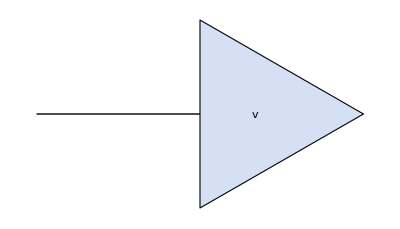

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{1,3}],ket["v",{3,0}]},ImageSize->{Automatic,25}]]
```

In component form:

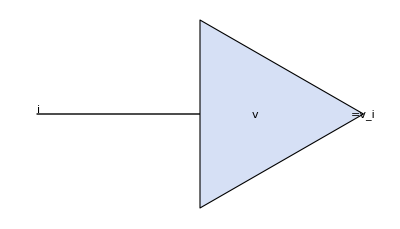

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{1,3}],ket["v",{3,0}],Text["\!\(i\)",{1,0},{-1,-0.5}],Text["\!\(=v\_i\)",{4,0},{-1,0}]},ImageSize->{Automatic,28}]]
```

Matrices are rank-2 tensors, represented by an object with two legs

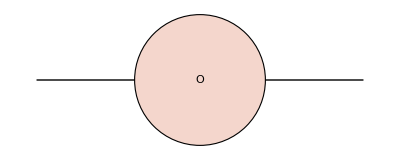

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,2}],opH["O",{0,0}]},ImageSize->{Automatic,25}]]
```

In component form:

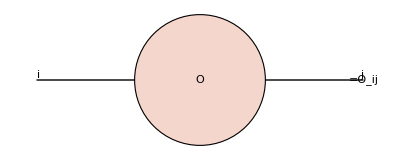

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,2}],opH["O",{0,0}],Text["\!\(i\)",{-2,0},{-1,-0.5}],Text["\!\(j\)",{2,0},{1,-0.5}],Text["\!\(=O\_\(ij\)\)",{2,0},{-1,0}]},ImageSize->{Automatic,27}]]
```

Tensor contraction: indices on internal legs are automatically summed over. For example, matrix-vector multiplication can be expressed as a tensor contraction.

w=Ô v

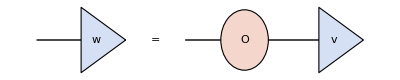

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,3}],opH["O"],ket["v",{3,0}],Line[{#,0}&/@{-7,-5}],ket["w",{-5,0}],Text["=",{-3,0}]},ImageSize->{Automatic,30}]]
```

In component form:

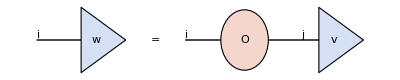

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{{Line[{#,0}&/@{-7,-5}],ket["w",{-5,0}],Text["\!\(i\)",{-7,0},{-1,-0.5}]},Text["=",{-3,0}],{Line[{#,0}&/@{-2,3}],opH["O"],ket["v",{3,0}],Text["\!\(i\)",{-2,0},{-1,-0.5}],Text["\!\(j\)",{2,0},{1,-0.5}]}},ImageSize->{Automatic,30}]]
```

w_i=∑_j O_(i,j)v_j

### Operator Algebra

#### Operator Product

Product (or composition) of two operators Ô and P̂ is a combined operator Ô P̂ that first applies P̂ to the sate then applies Ô (from right to left):

(Ô P̂)v=(Ô(P̂ v)).

Composing two operators ≏ multiplying two matrices.

Ô P̂≏(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)(P_11 | P_12 | ⋯
P_21 | P_22 | ⋯
⋮ | ⋮ | ⋱).

Prove Eq. (DisplayFormulaNumbered) using Eq. (DisplayFormulaNumbered).

Ô P̂=(∑_ij i O_ij j)(∑_kl k P_kl l)
=∑_(ij,kl) i O_ij jk P_kl l
=∑_(ij,kl) i O_ij δ_(j,k)P_kl l
=∑_ijl i O_ij P_jl l
=∑_il i(∑_j O_ij P_jl)l
=∑_ij i(∑_k O_ik P_kj)j.

Tensor network representation

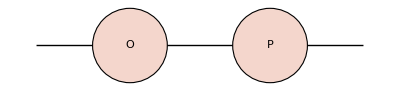

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-5,2}],opH["O",{-3,0}],opH["P",{0,0}]},ImageSize->{Automatic,25}]]
```

In component form:

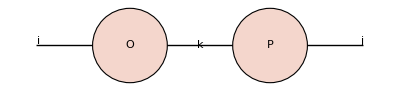

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-5,2}],Text["\!\(i\)",{-5,0},{-1,-0.5}],opH["O",{-3,0}],Text["\!\(k\)",{-1.5,0},{0,-0.5}],opH["P",{0,0}],Text["\!\(j\)",{2,0},{1,-0.5}]},ImageSize->{Automatic,27}]]
```

(O P)_ij=∑_k O_ik P_kj

Operator product is non-commutative in general, i.e.

Ô P̂≠P̂ Ô.

Example: product of Pauli operators

Multiplication table

| 𝟙 | (σ̂)^x | (σ̂)^y | (σ̂)^z
𝟙 | 𝟙 | (σ̂)^x | (σ̂)^y | (σ̂)^z
(σ̂)^x | (σ̂)^x | 𝟙 | ⅈ (σ̂)^z | -ⅈ (σ̂)^y
(σ̂)^y | (σ̂)^y | -ⅈ (σ̂)^z | 𝟙 | ⅈ (σ̂)^x
(σ̂)^z | (σ̂)^z | ⅈ (σ̂)^y | -ⅈ (σ̂)^x | 𝟙

Verify Eq. (DisplayFormulaNumbered) by multiplying Pauli matrices defined in Eq. (DisplayFormulaNumbered).

```mathematica
TableForm[Table[MatrixForm[PauliMatrix[a].PauliMatrix[b]],{a,0,3},{b,0,3}],TableHeadings->({#,#}&@{"𝟙","\!\(σ\^x\)","\!\(σ\^y\)","\!\(σ\^z\)"})]
```

| 𝟙 | σ^x | σ^y | σ^z
𝟙 | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | -ⅈ
ⅈ | 0) | (1 | 0
0 | -1)
σ^x | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (ⅈ | 0
0 | -ⅈ) | (0 | -1
1 | 0)
σ^y | (0 | -ⅈ
ⅈ | 0) | (-ⅈ | 0
0 | ⅈ) | (1 | 0
0 | 1) | (0 | ⅈ
ⅈ | 0)
σ^z | (1 | 0
0 | -1) | (0 | 1
-1 | 0) | (0 | -ⅈ
-ⅈ | 0) | (1 | 0
0 | 1)

Product of Pauli matrices (as the defining property of Pauli matrices)

(σ̂)^a(σ̂)^b=δ^ab 𝟙+ⅈ ϵ^abc(σ̂)^c,

where a,b,c=1,2,3 (stands for x,y,z).

Another version of Eq. (DisplayFormulaNumbered) using vector notation

(m·σ̂) (n·σ̂)=(m·n) 𝟙+ⅈ (m×n)·σ̂,

where m,n are three-component vectors (each component is a scalar).

The generalized vector σ̂ should be understood as a vector of matrices, or as a three-dimensional tensor.

Here m·σ̂ means

m·σ̂=m_1(σ̂)^1+m_2(σ̂)^2+m_3(σ̂)^3.

Use Eq. (DisplayFormulaNumbered) to show that the product of three Pauli operators follows 
(l·σ̂) (m·σ̂) (n·σ̂)=ⅈ l·(m×n)𝟙+ ((m·n)l-(l·n) m+(l·m) n)·σ̂ 
[Hint: the vector triple product formula will be useful 
l×(m×n)=(l·n)m-(l·m)n]

#### Commutator

Commutator of two operators Ô and P̂

[Ô,P̂]=Ô P̂-P̂ Ô.

Commutator is antisymmetric, [Ô,P̂]=-[P̂,Ô].

As a result, commutator of an operator with itself always vanishes [Ô,Ô]=0.

If the commutator vanishes [Ô,P̂]=0, we say that the two operators Ô and P̂ commute, i.e. Ô P̂=P̂ Ô (operators can pass though each other as if they were numbers) ⇒ it does not matter which operator is applied first, the consequence will be the same.

Example: dressing up to school.

A: put on the socks,

B: put on the shoes,

C: put on the hat,

A and B do not commute (changing the order leads to different result). But A and C commute, B and C also commute (changing the order does not affect the result).

Useful rules to evaluate commutators

Bi-linearity

[Ô,P̂+Q̂]=[Ô,P̂]+[Ô,Q̂],
[Ô+P̂,Q̂]=[Ô,Q̂]+[P̂,Q̂].

Prove Eq. (DisplayFormulaNumbered).

Prove the right linearity:

[Ô,P̂+Q̂]=Ô (P̂+Q̂)-(P̂+Q̂)Ô
=Ô P̂+Ô Q̂-P̂ Ô-Q̂ Ô
=Ô P̂-P̂ Ô+Ô Q̂-Q̂ Ô
=[Ô,P̂]+[Ô,Q̂].

Similar prove for the left linearity.

Product rules

[Ô,P̂ Q̂]=[Ô,P̂]Q̂+P̂ [Ô,Q̂],
[Ô P̂,Q̂]=[Ô,Q̂]P̂+Ô [P̂,Q̂].

Prove Eq. (DisplayFormulaNumbered).

[Ô,P̂ Q̂]=Ô P̂ Q̂-P̂ Q̂ Ô
=Ô P̂ Q̂-P̂ Ô Q̂+P̂ Ô Q̂-P̂ Q̂ Ô
=(Ô P̂ -P̂ Ô)Q̂+P̂ (Ô Q̂-Q̂ Ô)
=[Ô,P̂]Q̂+P̂ [Ô,Q̂]

Similarly for the other line.

Jacobi identity (as a replacement of associative law)

[Ô,[P̂,Q̂]]+[P̂,[Q̂,Ô]]+[Q̂,[Ô,P̂]]=0,
[[Ô,P̂],Q̂]+[[P̂,Q̂],Ô]+[[Q̂,Ô],P̂]=0.

Example: Commutators of Pauli operators

[(σ̂)^x,(σ̂)^y]=2ⅈ (σ̂)^z,
[(σ̂)^y,(σ̂)^z]=2ⅈ (σ̂)^x,
[(σ̂)^z,(σ̂)^x]=2ⅈ (σ̂)^y.

Or more compactly as

[(σ̂)^a,(σ̂)^b]=2ⅈ ϵ^abc(σ̂)^c,

for a,b,c=1,2,3 (stand for x,y,z). This can be considered as the defining algebraic properties of single-qubit operators (Pauli matrices). Or even more compactly using the cross product of vectors

σ̂×σ̂=2ⅈ σ̂.

#### Operator Function

Operator power. nth power of an operator Ô is the composition of Ô by n times.

(Ô)^n=Ô Ô…(n times)…Ô.

Operator function. Given a function f(x) that admits Taylor expansion

f(x)=∑_n c_n x^n,

the corresponding operator function is defined as

f(Ô)=∑_n c_n(Ô)^n,

with the same set of coefficients c_n.

f(Ô) is still an operator that can act on states in ℋ.

Operator exponential. Given the exponential function

ⅇ^x=1+x+x^2/(2!)+…=∑_(n=0)^∞ 1/(n!)x^n,

the exponential of an operator is defined as

ⅇ^(Ô)=1+Ô+(Ô)^2/(2!)+…=∑_(n=0)^∞ 1/(n!)(Ô)^n,

Note: exponentiating an matrix is NOT exponentiating each of the matrix element.

Example: exponentiating a Pauli matrix

Given (σ̂)^y≏(0 | -ⅈ
ⅈ | 0), 
show that the matrix representation of ⅇ^(ⅈ θ (σ̂)^y) is 
ⅇ^(ⅈ θ (σ̂)^y)≏(cos θ | sin θ
-sin θ | cos θ).

Method I: Mathematica

ⅇ^(ⅈ θ (σ̂)^y)≏e^(0 | θ
-θ | 0)=(cos θ | sin θ
-sin θ | cos θ).

```mathematica
MatrixExp[{{0,θ},{-θ,0}}]
```

{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}

Method II: Taylor expansion.

ⅇ^(ⅈ θ (σ̂)^y)=∑_n 1/(n!)(ⅈ θ (σ̂)^y)^n
=∑_n (ⅈ θ)^n/(n!)((σ̂)^y)^n

Note that

((σ̂)^y)^n=Piecewise[{{𝟙, if n is even,}, {(σ̂)^y, if n is odd.}}]

So

ⅇ^(ⅈ θ (σ̂)^y)=∑_m (ⅈ θ)^(2m)/((2m)!)((σ̂)^y)^(2m)+∑_m (ⅈ θ)^(2m+1)/((2m+1)!)((σ̂)^y)^(2m+1)
=∑_m (ⅈ θ)^(2m)/((2m)!)𝟙+∑_m (ⅈ θ)^(2m+1)/((2m+1)!)(σ̂)^y
=cos θ 𝟙+ⅈ sin θ (σ̂)^y
≏(cos θ | sin θ
-sin θ | cos θ).

Use the definition Eq. (DisplayFormulaNumbered) to prove that 
exp(ⅈ θ n·σ̂)=cos(θ)𝟙+ⅈ sin(θ) n·σ̂ 
given that n is a 3-component real unit vector.

#### Operator Trace

The trace of an operator Ô is defined as

Tr Ô=∑_i i Ô i.

The result is a scalar.

On the matrix level, taking the trace is simply summing over diagonal matrix elements

Tr(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)=O_11+O_22+…=∑_i O_(i,i).

Tensor network representation (tracing = closing the legs)

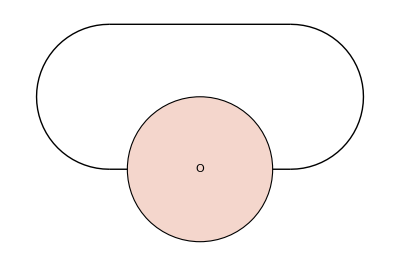

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-1,1}],Line[{#,1.6}&/@{-1,1}],Circle[{-1,0.8},0.8,{π/2,3π/2}],Circle[{1,0.8},0.8,{-π/2,π/2}],opH["O",{0,0}],(*Text["\!\(i\)",{1,0},{-1,-0.9}]*)},ImageSize->{Automatic,36}]]
```

Linear property: trace is a linear functional of operators.

Tr (α Ô+β P̂)=a Tr Ô+β Tr P̂.

Cyclic property: the trace of a product of operators is invariant under the cyclic permutation of the operators.

Tr (Ô P̂)=Tr (P̂ Ô),
Tr (Ô P̂ Q̂)=Tr (P̂ Q̂ Ô)=Tr (Q̂ Ô P̂),
…

Prove Eq. (DisplayFormulaNumbered).

The trick is to insert the resolution of identity 𝟙=∑_i ii.

Tr (Ô P̂)=∑_i i Ô P̂ i
=∑_(i,j) i Ô jj P̂ i
=∑_(i,j) j P̂ ii Ô j
=∑_j j P̂ Ô j
=Tr (P̂ Ô).

This property can be generalized to the product of more operators using the associativity of operator product. For example,

Tr (Ô P̂ Q̂)=Tr ((Ô P̂)Q̂)=Tr (Q̂(Ô P̂))=Tr (Q̂ Ô P̂).

Example: trace of Pauli operators

Pauli operators are traceless.

Tr (σ̂)^x=Tr (σ̂)^y=Tr (σ̂)^z=0.

This is true for a Pauli operator along any direction

Tr n·σ̂=0.

### Projection Operators

#### Projectors

State projector: the projection operator onto a state v

(𝒫̂)_v=vv.

Such that for any state u, applying the projection operator (𝒫̂)_v, the result is the projection of u along v

(𝒫̂)_v u=vvu.

Example: analog in the real vector space

```mathematica
Block[{θ=π/3},
Graphics[{{AbsoluteThickness[1],Gray,{Dashed,Line[{{Cos[θ],0},{Cos[θ],Sin[θ]}}]},Translate[Line[0.07{{1,0},{1,1},{0,1}}],{Cos[θ],0}],Circle[{0,0},0.1,{0,θ}]},Text["θ",{0.1,0},{-1,-0.8}],{Arrowheads[0.08],Arrow[{{0,0},#}],Text[#2,#1,#3]}&@@@{{{1,0},"\!\(v\)",{-1,0}},{{Cos[θ],Sin[θ]},"\!\(u\)",{0,-0.5}},{{Cos[θ],0},"\!\(v cos θ\)",{0,1}}}
},ImageSize->120]]
```

-Graphics-

u and v are two unit vectors, the projection of u on v is given by

v cos θ=v (v·u).

Basis projector: the projection operator onto a basis state i

(𝒫̂)_i=ii.

Basis projectors satisfies the following properties

(𝒫̂)_i^2=(𝒫̂)_i,
(𝒫̂)_i(𝒫̂)_j=0    if i≠j.

Or more compactly written as

(𝒫̂)_i(𝒫̂)_j=δ_ij(𝒫̂)_i.

Verify Eq. (DisplayFormulaNumbered), following the definition Eq. (DisplayFormulaNumbered).

Recall ij=δ_ij, i.e. ii=1 and ij=0 (if i≠j)

(𝒫̂)_i^2=iiii
=ii
=(𝒫̂)_i.

(𝒫̂)_i(𝒫̂)_j=iijj
=^(i≠j)i0j
=0.

Given the one-hot representation of orthonormal basis

1≏(1
0
0
⋮), 2≏(0
1
0
⋮), ….

Matrix representations of the corresponding basis projectors are

(𝒫̂)_1≏(1 |   |   |  
  | 0 |   |  
  |   | 0 |  
  |   |   | ⋱), (𝒫̂)_2≏(0 |   |   |  
  | 1 |   |  
  |   | 0 |  
  |   |   | ⋱), ….

Subspace projector: the projection operator onto a subspace. Suppose a subspace ℋ_1 is spanned by a set of orthonormal basis ℬ_1⊆ℬ, its projector is

(𝒫̂)_ℋ_1=∑_(i∈ℬ_1) ii.

Dimension of the subspace ℋ_1 is given by the trace of its projector (as it counts the number of basis states in ℬ_1)

Tr (𝒫̂)_ℋ_1=dim ℋ_1.

Completeness relation: full Hilbert space projector ≡ identity operator

(𝒫̂)_ℋ=∑_(i∈ℬ) ii=𝟙.

Recall Eq. (DisplayFormulaNumbered) that 𝟙=∑_(i,) ii. Hilbert space dimension is given by

dim ℋ=Tr (𝒫̂)_ℋ=Tr 𝟙.

Consider a Hilbert space ℋ spanned by three vectors 
x≏(1
0
0), y≏(0
1
0), z≏(0
0
1). 
Let ℋ_∥=span{x,y} and ℋ_⊥=span{z} be complementary subspaces.
(i) Construct the subspace projectors (𝒫̂)_(ℋ_∥) and (𝒫̂)_(ℋ_⊥) and represent them as 3×3 matrices (in the {x,y,z} basis).
(ii) For any v∈ℋ, show that v_∥=(𝒫̂)_(ℋ_∥)v and v_⊥=(𝒫̂)_(ℋ_⊥)v give the subspace decomposition of v such that  v=v_∥+v_⊥ with v_∥∈ℋ_∥ and v_⊥∈ℋ_⊥.

#### Quantum State Collapse*

What happens when we observe a quantum system?

Observing a quantum system can be viewed as a hypothesis testing.

Given the prior knowledge that a quantum system is described by a state v.

An observer comes with an objective to test the hypothesis that "the quantum system is in a target state u".

For this purpose, two projection operators are defined

(𝒫̂)_u=uu, (projector to the state u)
(𝒫̂)_(ū)=𝟙-(𝒫̂)_u.  (projector to the complement subspace)

Quantum mechanics predicts that the observation will accept the hypothesis with the probability

p(u|v)=v(𝒫̂)_u v=(|uv|)^2,

and reject the hypothesis with the (complement) probability

p(ū|v)=v(𝒫̂)_(ū)v=1-(|uv|)^2.

After observation, if the hypothesis is accepted (the state u is observed), we must update our knowledge about the quantum system to the posterior knowledge described by the state u. In this sense, the original quantum state v collapses to

v→u=((𝒫̂)_u v)/(√(p(u|v)))=((𝒫̂)_u v)/(√(v(𝒫̂)_u v)).

However, if the hypothesis is rejected (the state u is not observed), we must also update our posterior knowledge by collapsing to

v→((𝒫̂)_(ū)v)/(√(p(ū|v)))=((𝒫̂)_(ū)v)/(√(v(𝒫̂)_(ū)v)).

Verify Eq. (DisplayFormulaNumbered), Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Verify Eq. (DisplayFormulaNumbered):

v(𝒫̂)_u v=vuuv=(|uv|)^2.

Verify Eq. (DisplayFormulaNumbered):

v(𝒫̂)_(ū)v=v𝟙-(𝒫̂)_u v=vv-v(𝒫̂)_u v=1-(|uv|)^2.

Verify Eq. (DisplayFormulaNumbered):

((𝒫̂)_u v)/(√(v(𝒫̂)_u v))=uuv/(√((|uv|)^2))=uv/(|uv|)u,

since uv/|uv| is only an overall phase factor of the quantum state, the resulting state is identical to the state u.

Summary: the collapse of any prior state v to the target state u is described by the state projection operator (𝒫̂)_u (associated with the target state).

As an observable, it gives the probability p(u|v) for the state collapse to happen.

As an operator, it implements the state collapse v→u (Note: this is not a linear operation, as v appears on both the numerator and the denominator).

Example: Observing a qubit

Given the prior knowledge that a qubit is in the state

ψ≏(ψ_0
ψ_1).

The probability p(0|ψ) to observe the qubit in the state 0

0≏(1
0)⇒(𝒫̂)_0=00=(1 | 0)(1
0)=(1 | 0
0 | 0)

is given by

p(0|ψ)=ψ(𝒫̂)_0 ψ
=(ψ_0^* | ψ_1^*)(1 | 0
0 | 0)(ψ_0
ψ_1)
=ψ_0^*ψ_0=(|ψ_0|)^2.

If 0 state is indeed observed, the quantum state should collapse to

((𝒫̂)_0 ψ)/(√(p(0|ψ)))≏1/(√((|ψ_0|)^2))(1 | 0
0 | 0)(ψ_0
ψ_1)
=ψ_0/(|ψ_0|)(1
0)∼(1
0)≏0.

## Measurement

### Hermitian Operators

#### Hermitian Conjugate

We have explained how an operator Ô acts on a ket state v, what about its action on the bra state v?

| ket | bra (dual)
Hilbert space | ℋ | ℋ^*
basis | ℬ={i} | ℬ^*={i}
state | v=∑_i v_i i | v=∑_i v_i^*i
vector | (v_1
v_2
⋮) | (v_1^* | v_2^* | ⋯)
component | v_i=iv | v_i^*=vi
operator | Ô=∑_(i,j) i O_(i,j)j | (Ô)^†=∑_(i,j) i O_(j,i)^*j
matrix | (O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱) | (O_11^* | O_21^* | ⋯
O_12^* | O_22^* | ⋯
⋮ | ⋮ | ⋱)
component | O_(i,j)=i Ô j | O_(i,j)^*=j(Ô)^†i
action | w=Ô v | w=v(Ô)^†

Just like the bra v is the dual of the ket u, the Hermitian conjugate operator (Ô)^† is the dual of the original operator Ô, such that

if the operator Ô takes v to w:

Ô | : | ℋ | → | ℋ
  |   | v | ↦ | w=Ô v

then the operator (Ô)^† takes v to w:

(Ô)^† | : | ℋ^* | → | ℋ^*
  |   | v | ↦ | w=v(Ô)^†

Tensor network representation

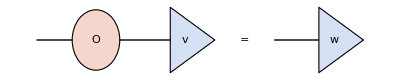

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,3}],opH["O"],ket["v",{3,0}],Line[{#,0}&/@{6,8}],ket["w",{8,0}],Text["=",{5,0}]},ImageSize->{Automatic,30}]]
```

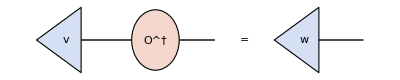

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{2,-3}],opH["O\^†"],bra["v",{-3,0}],Line[{#,0}&/@{5,7}],bra["w",{5,0}],Text["=",{3,0}]},ImageSize->{Automatic,30}]]
```

Given an orthonormal basis  ℬ={i:i=1,2,…} of the Hilbert space ℋ, if Ô is given by

Ô=∑_(i,j) i O_(i,j)j,

then (Ô)^† should be given by

(Ô)^†=∑_(i,j) i O_(j,i)^*j.

Verify that Eq. (DisplayFormulaNumbered) is consistent with the definition Eq. (DisplayFormulaNumbered).

Dual to Eq. (DisplayFormulaNumbered), suppose

v=∑_i v_i^*i, w=∑_i w_i^*i,
(Ô)^†=∑_(i,j) i O_(j,i)^*j.

Then to give w=v(Ô)^†

v(Ô)^†=(∑_i v_i^*i)(∑_(j,k) j O_(k,j)^*k)
=∑_(i,j,k) v_i^*O_(k,j)^*ijk
=∑_(i,j,k) v_i^*O_(k,j)^*δ_(i,j)k
=∑_(,j,k) v_j^*O_(k,j)^*k
=∑_(i,j) v_j^*O_(i,j)^*i,

compare with w in Eq. (DisplayFormulaNumbered), we must have

w_i^*=∑_(i,j) v_j^*O_(i,j)^*.

Take complex conjugation on both sides, we obtain

w_i=∑_j O_(i,j)v_j,

which is consistent with w=Ô v as verified in Eq. (DisplayFormulaNumbered).

In terms of matrix representation, the Hermitian conjugate acts as

matrix transpose (interchanges the rows and columns),

followed by complex conjugation of each matrix element.

(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)^†=(O_11^* | O_21^* | ⋯
O_12^* | O_22^* | ⋯
⋮ | ⋮ | ⋱).

How to think of it: Hermitian conjugate ∼ a generalization of complex conjugate from complex numbers to matrices.

Hermitian conjugate has the following properties:

Duality: suppose Ô is an operator

((Ô)^†)^†=Ô.

Linearity: suppose Ô and P̂ are operators, α and  β are complex numbers,

(α Ô+β P̂)^†=α^*(Ô)^†+β^*(P̂)^†.

Transpose Property: suppose Ô and P̂ are operators

(Ô P̂)^†=(P̂)^†(Ô)^†.

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-5,2}],opH["O",{-3,0}],opH["P",{0,0}]},ImageSize->{Automatic,25}]]
```

-Graphics-

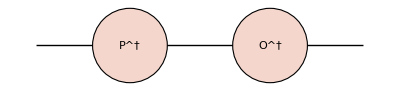

```mathematica
Block[{ket,bra,opH,opU},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-5,2}],opH["P\^†",{-3,0}],opH["O\^†",{0,0}]},ImageSize->{Automatic,25}]]
```

Prove the property Eq. (DisplayFormulaNumbered).

Suppose

Ô=∑_(i,j) i O_(i,j)j, P̂=∑_(i,j) i P_(i,j)j,

then

(Ô P̂)^†=(∑_ij i(∑_k O_ik P_kj)j)^†
=∑_ij j(∑_k O_ik^*P_kj^*)i
=∑_(ij,k) O_ik^*P_kj^*ji
=∑_(ij,k,l) O_ik^*P_lj^*jlki
=∑_(ij,k,l) j P_lj^*lk O_ik^*i
=(∑_(j,l) j P_lj^*l)(∑_ik k O_ik^*i)
=(P̂)^†(Ô)^†.

#### Hermitian Operator

Real numbers play a special role in physics. The results of any measurements are real. If in quantum mechanics, physical observables are represented by operators, how do we impose the “real” condition on operators?

A real number is a number whose complex conjugation is itself.

A real operator Hermitian operator is an linear operator whose Hermitian conjugate is itself.

An operator Ô=∑_(i,j) i O_(i,j)j is call Hermitian, if

Ô=(Ô)^†,

or in terms of matrix elements,

O_ij=O_ji^*.

Given a complex number z, real part: Re z=(z+z^*)/2, imaginary part: Im z=(z-z^*)/(2ⅈ). Similarity, given a generally non-Hermitian operator P̂

Re P̂=1/2(P̂+(P̂)^†), Im P̂=1/(2ⅈ)(P̂-(P̂)^†).

Both Re P̂ and Im P̂ are Hermitian operators.

#### Eigenvalues and Eigenvectors (General)

Given an operator Ô, the eigenvectors O_k are a set of special vectors, on which the operator Ô acts as a scalar multiplication

Ô O_k=O_k O_k,  (k=1,2,…)

and the corresponding scalars  O_k are called the eigenvalues (of the corresponding eigenvectors).

Eq. (DisplayFormulaNumbered) is called the eigen equation of an operator Ô.

The eigenvalues can be found by solving the algebraic (polynomial) equation for O∈ℝ

det(Ô-O 𝟙)=0.

For each solution of eigenvalue  O=O_k, the corresponding eigenvector O_k is found by solving the linear equation

(Ô-O_k 𝟙)O_k=0.

Use Mathematica to solve the eigen problem (recommended)

```mathematica
Eigensystem[{{1,-1},{1,1}}]
```

{{1+ⅈ,1-ⅈ},{{ⅈ,1},{-ⅈ,1}}}

Degeneracy: an eigenvalue O_k of an operator Ô is called g_k-fold degenerated, if there are exactly g_k linearly independent eigenvectors corresponding to the same eigenvalue

Ô O_k,m=O_k O_k,m, (m=1,2,…,g_k).

Since any linear combination of the degenerated eigenvectors

∑_(m=1)^g_k α_m O_k,m, (with α_k∈ℂ)

is still an eigenvector of the same eigenvalue O_k, thus the degenerated eigenvectors forms a degenerated subspace ℋ_(O=O_k) (the subspace of all eigenvectors of the same eigenvalue O_k)

ℋ_(O=O_k)=span{O_k,m:m=1,2,…,g_k}.

Eigen projector: projection operator to the degenerated subspace associated with an eigenvalue O_k

(𝒫̂)_(O=O_k)=∑_(m=1)^g_k O_k,mO_k,m.

#### Eigenvalues and Eigenvectors (Hermitian Operator)

What is special about Hermitian operators?

Suppose Ô=(Ô)^† is a Hermitian operator and

Ô O_k=O_k O_k, (k=1,2,…).

Eigenvalues are real.

Ô=(Ô)^†⇒O_k∈ℝ.

Eigenvectors form a complete set of basis. (Any vector  can be expanded as a sum of these eigenvectors.)

Eigenvectors of different eigenvalues are orthogonal (automatically)

O_k≠O_l⇒O_kO_l=0.

Eigenvectors of the same eigenvalue can be made orthogonal (by orthogonalization, e.g. Gram-Schmidt procedure).

```mathematica
Orthogonalize[{{1,2},{3,4}}]
```

{{1/(√5),2/(√5)},{2/(√5),-1/(√5)}}

For bounded Hermitian operators (e.g. finite matrices in finite dimensional Hilbert space), eigenvectors can be normalized.

Prove Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Suppose

Ô O_k=O_k O_k,

Ô O_l=O_l O_l.

Take Hermitian conjugate on both sides of Eq. (DisplayFormulaNumbered),

O_k(Ô)^†=O_k Ô=k O_k^*,

we have

O_k Ô O_l=O_k^*O_kO_l,
O_k Ô O_l=O_l O_kO_l.

If k=l, Eq. (DisplayFormulaNumbered) implies

O_k Ô O_k=O_k^*O_kO_k=O_k O_kk,

i.e. O_k^*=O_k, so O_k∈ℝ. This proves Eq. (DisplayFormulaNumbered).

If k≠l, Eq. (DisplayFormulaNumbered) implies

0=(O_k-O_l)O_kO_l.

If O_k!=O_l, Eq. (DisplayFormulaNumbered) implies O_kO_l=0. This proves Eq. (DisplayFormulaNumbered).

If O_k=O_l, then O_k and O_l are degenerated. Degenerated states can be arbitrarily recombined within the degenerate subspace to form a set of orthogonal basis.

Therefore each Hermitian operator Ô generates a complete set of orthonormal basis {O_k:k=1,2,…} for the Hilbert space ℋ, also called the eigenbasis of Ô.

Hermitian operator Ô can always be represented in its own eigenbasis, leading to the spectral decomposition

Ô=∑_k O_k O_k O_k.

Note: unlike a generic matrix representation Ô=∑_ij i O_ij j, in the spectral decomposition Eq. (DisplayFormulaNumbered), the summation only run through the eigenbasis once.

In the eigenbasis, the Hermitian operator is represented as a diagonal matrix.

Ô≏(O_1 |   |  
  | O_2 |  
  |   | ⋱).

So the procedure of bring the matrix representation to its diagonal form by transforming to its eigenbasis is called diagonalization. (We will discuss more about it later.)

More generally, when there are degeneracies, Eq. (DisplayFormulaNumbered) should be written to

Ô=∑_k ∑_(m=1)^g_k O_k,m O_k O_k,m
=∑_k O_k(𝒫̂)_(O=O_k),

where the eigen projector (𝒫̂)_(O=O_k) was defined in Eq. (DisplayFormulaNumbered).

The fact that all eigenvectors of Ô form a complete set of orthonormal basis can be rephrases as the following properties of eigen projectors

Orthonormality

(𝒫̂)_(O=O_k)(𝒫̂)_(O=O_l)=δ_(k,l)(𝒫̂)_(O=O_k).

Meaning that (𝒫̂)_(O=O_k)^2=(𝒫̂)_(O=O_k) and (𝒫̂)_(O=O_k)(𝒫̂)_(O=O_l)=0 if k≠l (i.e. O_k≠O_l).

Completeness

∑_k (𝒫̂)_(O=O_k)=(𝒫̂)_ℋ≡𝟙.

Example: Eigenvalues and eigenvectors of Pauli operators

Pauli matrices are 2×2 Hermitian matrices. Each one has two distinct eigenvalues, and two corresponding orthogonal eigenvectors.

opertor | (σ̂)^x |  | (σ̂)^y |  | (σ̂)^z | 
(matrix) | (0 | 1
1 | 0) |  | (0 | -ⅈ
ⅈ | 0) |  | (1 | 0
0 | -1) | 
eigenvalue | +1 | -1 | +1 | -1 | +1 | -1
eigenvector | + | - | ⅈ | ⅈ̄ | 0 | 1
(vector) | 1/(√2)(1
1) | 1/(√2)(1
-1) | 1/(√2)(1
ⅈ) | 1/(√2)(1
-ⅈ) | (1
0) | (0
1)
projector | ++ | -- | ⅈⅈ | ⅈ̄ⅈ̄ | 00 | 11
(matrix) | 1/2(1 | 1
1 | 1) | 1/2(1 | -1
-1 | 1) | 1/2(1 | -ⅈ
ⅈ | 1) | 1/2(1 | ⅈ
-ⅈ | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)

Spectral decompositions:

Pauli-x

(σ̂)^x=(𝒫̂)_(σ^x=+1)-(𝒫̂)_(σ^x=-1),

with projection operators

(𝒫̂)_(σ^x=+1)=++=(𝟙+(σ̂)^x)/2,
(𝒫̂)_(σ^x=-1)=--=(𝟙-(σ̂)^x)/2.

Pauli-y

(σ̂)^y=(𝒫̂)_(σ^y=+1)-(𝒫̂)_(σ^y=-1),

with projection operators

(𝒫̂)_(σ^y=+1)=ⅈⅈ=(𝟙+(σ̂)^y)/2,
(𝒫̂)_(σ^y=-1)=ⅈ̄ⅈ̄=(𝟙-(σ̂)^y)/2.

Pauli-z

(σ̂)^z=(𝒫̂)_(σ^z=+1)-(𝒫̂)_(σ^z=-1),

with projection operators

(𝒫̂)_(σ^z=+1)=00=(𝟙+(σ̂)^z)/2,
(𝒫̂)_(σ^z=-1)=11=(𝟙-(σ̂)^z)/2.

In general, the Pauli operator n·σ̂ along the direction of the unit vector n has the following spectral decomposition

n·σ̂=(𝒫̂)_(n·σ=+1)-(𝒫̂)_(n·σ=-1),

with the projection operators

(𝒫̂)_(n·σ=±1)=n·σ=±1n·σ=±1=(𝟙±n·σ̂)/2.

Prove Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Given that n·σ̂ is a 2×2 Hermitian matrix, it must have two real eigenvalues, denoted as λ_1 and λ_2. In the eigenbasis, n·σ̂ is represented as a diagonal matrix

n·σ̂≏(λ_1 | 0
0 | λ_2)

Notice that

λ_1+λ_2=Tr (n·σ̂)=0,
(λ_1^2 | 0
0 | λ_2^2)≏(n·σ̂)^2=𝟙,

we have

λ_1^2=λ_2^2=1⇒λ_1,λ_2=±1,
λ_1+λ_2=0⇒λ_1=-λ_2.

So the two eigenvalues of n·σ̂ must be +1 and -1, and the spectral decomposition must take the form of

n·σ̂=(𝒫̂)_(n·σ=+1)-(𝒫̂)_(n·σ=-1).

In the eigenbasis, without loss of generality, we can write

n·σ̂≏(1 | 0
0 | -1).

Now the projectors are represented as

(𝒫̂)_(n·σ=+1)≏(1 | 0
0 | 0), (𝒫̂)_(n·σ=-1)≏(0 | 0
0 | 1).

Comparing Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we conclude

(𝒫̂)_(n·σ=±1)=(𝟙±n·σ̂)/2.

To check this result, substitute Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered), we can see that the equation is consistent.

Assuming Ô is a Hermitian operator, use the spectral decomposition Eq. (DisplayFormulaNumbered) and the properties of projection operators to show that 
(i) The operator power can be expanded as (Ô)^n=∑_k O_k^n(𝒫̂)_(O=O_k).
(ii) More generally, the operator function f(Ô) defined in Eq. (DisplayFormulaNumbered) can be expanded as f(Ô)=∑_k f(O_k)(𝒫̂)_(O=O_k).

### Observables

#### Physical Observable

Postulate 2 (Observables): Physical observables of a quantum system are described by Hermitian operators (represented as Hermitian matrices) acting on the associated Hilbert space.

Consider a Hermitian operator Ô with eigenvalues O_k and eigenvectors O_k,m (m=1,2,…,g_k),

Ô=∑_k O_k(𝒫̂)_(O=O_k),

where the eigen projector is

(𝒫̂)_(O=O_k)=∑_(m=1)^g_k O_k,mO_k,m.

The operator Ô corresponds to a physical observable O in the sense that

All possible measurement outcomes (or observation values) of the observable O are given by (and only by) the eigenvalues O_k.

The measurement projects (collapses) the quantum state to the eigenspace ℋ_k of the corresponding measurement outcome O_k. The state collapse is implemented by the eigen projector (𝒫̂)_ℋ_k.

#### Measurement Postulate

Postulate 3 (Measurement): Given a quantum system in the state ψ and the observable O to be measured: 
(i) the probability to observe the measurement outcome O_k is p(O_k|ψ)=ψ(𝒫̂)_ℋ_k ψ, 
(ii) if O_k is observed, the state will collapse to (𝒫̂)_ℋ_k ψ/√(p(O_k|ψ)).

In quantum measurement, there is no way to tell for certain which outcome will be observed. There is only a conditional probability p(O_k|ψ) that we can compute.

Non-degenerated case: Suppose O_k has no degeneracy,

(𝒫̂)_ℋ_k=O_kO_k.

The probability to observe O_k is given by the squared overlap between the prior state ψ and the eigenstate O_k

p(O_k|ψ)=(|O_kψ|)^2.

After the measurement, if O_k is observed, the system collapses to the posterior state O_k

ψ⟶^(measure O, observe O_k)O_k.

These results are consistent with our previous discussions in Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) about quantum state collapse.

Degenerated case (generic): With degeneracy, the eigen projector is

(𝒫̂)_ℋ_k=∑_(m=1)^g_k O_k,mO_k,m.

The probability to observe O_k is given by the squared overlap between the prior state ψ and all eigenstates O_k,m in the degenerate subspace

p(O_k|ψ)=∑_(m=1)^g_k (|O_k,mψ|)^2.

After the measurement, if O_k is observed, the system collapses to the posterior state, given by a linear superposition of O_k,m

ψ⟶^(measure O, observe O_k)∑_(m=1)^g_k α_m O_k,m,

where the coefficients α_m are given by

α_m=(O_k,mψ)/(√(p(O_k|ψ))).

Derive Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

According to the measurement postulate, the measurement probability is given by

p(O_k|ψ)=ψ(𝒫̂)_ℋ_k ψ
=ψ(∑_(m=1)^g_k O_k,mO_k,m)ψ
=∑_(m=1)^g_k ψO_k,mO_k,mψ
=∑_(m=1)^g_k (|O_k,mψ|)^2.

Given the measurement outcome O_k, the state should collapse to

((𝒫̂)_ℋ_k ψ)/(√(p(O_k|ψ)))=1/(√(p(O_k|ψ)))(∑_(m=1)^g_k O_k,mO_k,m)ψ
=1/(√(p(O_k|ψ)))∑_(m=1)^g_k O_k,mO_k,mψ
=∑_(m=1)^g_k (O_k,mψ)/(√(p(O_k|ψ)))O_k,m.

therefore the coefficients α_m should be

α_m=(O_k,mψ)/(√(p(O_k|ψ))).

Let {1,2,3} be a set of orthonormal basis of a three-state system. Suppose the system is in the prior state ψ=1/(√3)(1+2+3).
Consider measuring the observable Ô=12+21-33 . 
(i) What are the possible measurement outcomes (observation values)?
(ii) What are the probabilities to observe each outcome?
(iii) What posterior states will the system collapse to after observing each outcome?

#### Expectation Value

Expectation value of an observable O, denoted as ⟨O⟩, is the averaged measurement outcome of O over many repeated experiments (with the same prior state ψ prepared each time).

According to the measurement postulate

⟨O⟩:=∑_k O_k p(O_k|ψ)
=∑_k O_k ψ(𝒫̂)_ℋ_k ψ.

Given Ô=∑_k O_k(𝒫̂)_ℋ_k, we conclude

⟨O⟩=ψ Ô ψ.

The answer is a real scalar (as Ô is Hermitian).

Represented as vectors and matrices,

⟨O⟩=(ψ_1^* | ψ_2^* | ⋯)(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)(ψ_1
ψ_2
⋮).

Tensor network representation

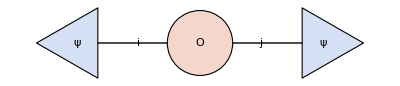

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-3,3}],bra["ψ",{-3,0}],Text["\!\(i\)",{-1.5,0},{0,-0.5}],opH["O"],Text["\!\(j\)",{1.5,0},{0,-0.5}],ket["ψ",{3,0}]},ImageSize->{Automatic,27}]]
```

⟨O⟩=∑_(i,j) ψ_i^*O_(i,j)ψ_j.

Alternatively, the expectation value can also be written as a trace of the product of the observable operator Ô and the state projector (𝒫̂)_ψ=ψψ [defined in Eq. (DisplayFormulaNumbered)]

⟨O⟩=Tr Ô (𝒫̂)_ψ.

The equivalence between Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) is self-evident from the tensor network diagrams

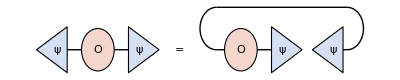

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Translate[{Line[{#,0}&/@{-2,2}],bra["ψ",{-2,0}],opH["O"],ket["ψ",{2,0}]},{-4,0}],Text["=",{0,0}],Translate[{Circle[{-3.2,0.8},0.8,{π/2,3π/2}],Line[{#,0}&/@{-3.2,0}],opH["O",{-2,0}],ket["ψ",{0,0}],bra["ψ",{2.5,0}],Line[{#,0}&/@{3,3.2}],Circle[{3.2,0.8},0.8,{-π/2,π/2}],Line[{#,1.6}&/@{3.2,-3.2}]},{5,0}]},ImageSize->{Automatic,38}]]
```

The advantage of this approach is to circumvent solving for ψ explicitly (sometimes the state projector is easier to construct than the state vector).

Let m and n be three-component real unit vectors. For a qubit, consider measuring n·σ on the m·σ=+1 state.
(i) What is the probability to observe n·σ=+1?
(ii) What is the expectation value of the operator n·σ̂ on the state  m·σ=+1?
[Express your results in terms of m and n.]

### Sequential Measurements

#### Commuting Operators

Commuting operators share common eigenbasis, and the converse is also true.

Commuting operators: Two operators Â and B̂ commute, if Â B̂=B̂ Â (operators can commute through each other), i.e.

[Â,B̂]=0.

(Here 0 denotes the zero operator, a matrix whose elements are all zeros.)

Common eigenbasis: Two operators Â and B̂ share a common eigenbasis, if there exist a complete set of basis ℬ={A_k,B_k:k=1,2,…,dim ℋ} such that both operators are diagonal in the basis ℬ, i.e.

Â A_k,B_k=A_k A_k,B_k,
B̂ A_k,B_k=B_k A_k,B_k.

Idea: commuting operators can pass through each other as if they were numbers. If Â and B̂ share a common eigenbasis, when acting on their common eigenvectors, they behave like numbers (by their eigenvalues),

Â B̂ A_k,B_k=A_k B_k A_k,B_k=B_k A_k A_k,B_k=B̂ Â A_k,B_k.

Any state v=∑_k α_k A_k,B_k is just a linear superposition of the basis states, so the behavior of Â B̂ v=B̂ Â v is generic for all states, thus the equality can be promoted from the state level to the operator level Â B̂=B̂ Â, i.e. the two operators commute.

Example: Finding common eigenbasis of commuting operators. Consider two Hermitian operators

Â≏(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0), B̂≏(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0).

```mathematica
A={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};
B={{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,-ⅈ,0}};
A//MatrixForm
B//MatrixForm
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0)

It can be checked that Â and B̂ commute (by showing that [Â,B̂]=0)

```mathematica
A.B-B.A//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

They must share a set of common eigenbasis. How to find that? - Strategy: using a random algorithm.

Construct a random operator Ĥ=a Â+b B̂ by combining Â and B̂ with random numbers a and b.

```mathematica
(H=0.2A+0.5B)//MatrixForm
```

(0. | 0.-0.5 ⅈ | 0. | 0.2
0.+0.5 ⅈ | 0. | 0.2 | 0.
0. | 0.2 | 0. | 0.+0.5 ⅈ
0.2 | 0. | 0.-0.5 ⅈ | 0.)

Find the eigenbasis of Ĥ

```mathematica
{vals,vecs}=Chop@Eigensystem[H]
```

{{0.7,-0.7,0.3,-0.3},{{-0.5,0.-0.5 ⅈ,0.-0.5 ⅈ,-0.5},{-0.5,0.+0.5 ⅈ,0.-0.5 ⅈ,0.5},{-0.5,0.-0.5 ⅈ,0.+0.5 ⅈ,0.5},{-0.5,0.+0.5 ⅈ,0.+0.5 ⅈ,-0.5}}}

1=1/2(-1
-ⅈ
-ⅈ
-1), 2=1/2(-1
+ⅈ
-ⅈ
+1), 3=1/2(-1
-ⅈ
+ⅈ
+1), 4=1/2(-1
+ⅈ
+ⅈ
-1)

With probability 1, the eigenbasis of Ĥ is the common eigenbasis of Â and B̂, such that both operators are diagonal in this basis.

```mathematica
Chop[vecs.A.ConjugateTranspose[vecs]]//MatrixForm
Chop[vecs.B.ConjugateTranspose[vecs]]//MatrixForm
```

(1. | 0 | 0 | 0
0 | -1. | 0 | 0
0 | 0 | -1. | 0
0 | 0 | 0 | 1.)

(-1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | -1. | 0
0 | 0 | 0 | 1.)

We might rename the eigenvectors by their eigenvalues under both Â and B̂,

1→+1,-1, 2→-1,+1,3→-1,-1,4→+1,+1;

such that the eigen equations can be written in the standard form Eq. (DisplayFormulaNumbered)

Â A_k,B_k=A_k A_k,B_k,
B̂ A_k,B_k=B_k A_k,B_k;

with the eigenvalues arranged as

(A_1,A_2,A_3,A_4)=(+1,-1,-1,+1),
(B_1,B_2,B_3,B_4)=(-1,+1,-1,+1).

#### Compatible Observables

Suppose A and B are two observables and we perform the following sequential measurements on a single quantum system:

measure A,

measure B,

measure A.

We say that A and B are compatible observables, iff the result of 3 is always certain to be the same as the result of 1.

In general, this will not be the case.

In step 1, we measure A and suppose that we obtain the outcome A_1 (as one eigenvalue of Â), the system has collapse to the state A_1.

In step 2, we measure B and suppose that we obtain the outcome B_1 (as one eigenvalue of B̂), the system will collapse to the state B_1. (This will happen with probability (|B_1A_1|)^2).

In step 3, we measure A again. There is no guarantee that the previous outcome A_1 will appear again. Instead we may obtain a different outcome A_2 with probability (|A_2B_1|)^2 in general.

In order to obtain A_1 again with probability 1, we must require

(|A_1B_1|)^2=1,

i.e. A_1 and B_1 labels the identical state. Since A_1 is an eigenstate of Â with eigenvalue A_1 and B_1 is an eigenstate of B̂ with eigenvalue B_1, the state must be a common eigenstate A_1,B_1 of both Â and B̂, s.t.

Â A_1,B_1=A_1 A_1,B_1,
B̂ A_1,B_1=B_1 A_1,B_1.

For this scenario to always happen regardless the choice of (A_1,B_1), Â and B̂ share a set of common eigenbasis A_k,B_k (k=1,2,…,dim ℋ).

Conclusion: Given two observables A and B, described by Hermitian operators Â and B̂, then following statements are equivalent

A and B are compatible observables;

Â and B̂ share common eigenbasis;

Â and B̂ are commuting operators: [Â,B̂]=0.

### Repeated Measurements

#### Statistics of Measurements

Repeated measurements: Given a state ψ and an observable O, perform the following repeatedly:

prepare a quantum system in the state ψ (e.g. by measuring (𝒫̂)_ψ=ψψ and post-select);

measure O on the state ψ (the outcome O_k will be obtained with probability p(O_k|ψ)=ψ O_k ψ)

discard the quantum system (or reset the state).

This will collect an ensemble of measurement outcomes

{O_k:p(O_k|ψ)=ψ O_k ψ}.

With this ensemble, we can define the following statistics

Mean (expectation value):

⟨O⟩=∑_k O_k p(O_k|ψ)=ψ Ô ψ.

Variance (2nd moment):

varO=∑_k (O_k-⟨O⟩)^2 p(O_k|ψ)=(ψ(Ô-⟨O⟩𝟙))^2 ψ.

Introduce the observable ΔO (the deviation of O from its expectation value)

ΔO=O-⟨O⟩𝟙,

The variance can be written as var O=⟨(ΔO)^2⟩.

Standard deviation: characterizes the uncertainty of the measurement of O

stdO=(varO)^(1/2)=⟨(ΔO)^2⟩^(1/2).

#### Uncertainty Relation

Uncertainty Relation: for any pair of observables A and B measured on any given state (repeatedly),

(std A)(std B)≥1/2|⟨[A,B]⟩|.

In words, the product of the uncertainties cannot be smaller than half of the magnitude of the expectation value of the commutator.

For commuting observables ([A,B]=0), (std A)(std B)≥0, it is possible to have std A=std B=0 simultaneously, i.e. A and B can be jointly measured with perfect certainty.

For non-commuting observables, there exists a state on which |⟨[A,B]⟩|≠0. Then on such state, it is impossible to have std A=std B=0 simultaneously, i.e. A and B can not be jointly measured with certainty.

Proof of the uncertainty relation:

Suppose Â and B̂ are Hermitian operators. Let ϕ=(Â+ⅈ x B̂)ψ. For any choice of x∈ℝ,

ψ(Â-ⅈ x B̂)(Â+ⅈ x B̂)ψ=ϕϕ≥0.

On the other hand,

ψ(Â-ⅈ x B̂)(Â+ⅈ x B̂)ψ
=ψ(Â)^2+ⅈ x [Â,B̂]+x^2(B̂)^2 ψ
=⟨B^2⟩x^2+ⅈ⟨[A,B]⟩x+⟨A^2⟩≥0.

The quadratic equation ⟨B^2⟩x^2+ⅈ⟨[A,B]⟩x+⟨A^2⟩=0 has no (or only one) real root, implying that its discriminant Δ must be negative (or zero), i.e.

Δ=(ⅈ⟨[A,B]⟩)^2-4⟨B^2⟩⟨A^2⟩≤0.

Therefore for any A,B on any state ψ,

⟨A^2⟩^(1/2)⟨B^2⟩^(1/2)≥1/2|⟨[A,B]⟩|.

The uncertainty relation Eq. (DisplayFormulaNumbered) can be shown by replacing A→ΔA and B→ΔB.

Suppose A and B are Hermitian operators.
(i) Show that ⟨A^2⟩,  ⟨B^2⟩ and  ⅈ⟨[A,B]⟩ are real.
(ii) Show that [ΔA,ΔB]=[A,B].

## Dynamics

### Unitary Operators

#### Basis Transformation

Suppose we have two sets of orthonormal basis of the same Hilbert space ℋ

ℬ={i:i=1,2,…,dim ℋ},
ℬ'={i':i=1,2,…,dim ℋ}.

For example, the eigen basis of (σ̂)^x v.s. that of (σ̂)^z.

The same state v can have different vector representations in different bases

v_i=iv, v'_i=i' v.

The same operator Ô can have different matrix representations in different bases

O_ij=i Ô j, O'_ij=i' Ô j'.

How are representations in different bases related? - Basis transformation. Basis transformation from ℬ to ℬ' is describe by a matrix U with the matrix element

U_ij=i' j.

such that the representation in the new basis is related to that in the old basis by

v'_i=∑_j U_ij v_j,
O'_ij=∑_(k,l) U_ik O_kl U_jl^*.

Using Eq. (DisplayFormulaNumbered) to prove that Eq. (DisplayFormulaNumbered) is compatible with Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Basis transformation for state

v'_i=∑_j U_ij v_j
=∑_j i' jjv
=i' 𝟙v
=i' v.

Basis transformation for operator

O'_ij=∑_(k,l) U_ik O_kl U_jl^*
=∑_(k,l) i' kk Ô ll j'
=i' 𝟙 Ô 𝟙 j'
=i' Ô j'.

In quantum mechanics, every operator is a matrix, and every matrix is an operator. So does the basis transformation matrix.

Û=∑_i ii'.

Check that the matrix element of Û in Eq. (DisplayFormulaNumbered) is indeed given by Eq. (DisplayFormulaNumbered), when represented in either the basis ℬ or ℬ'.

When represented in ℬ, the matrix element of Û should be given by Eq. (DisplayFormulaNumbered) as

U_ij=i Û j
=∑_k ik k' j
=∑_k δ_ik k' j
=i' j.

When represented in ℬ',

U'_ij=i' Û j'
=∑_k i' k k' j'
=∑_k i' k δ_kj
=i' j.

It turns out that the matrix elements U'_ij=U_ij are the same regardless of basis (this is a special property for the basis transformation matrix between two orthonormal bases).

Û in Eq. (DisplayFormulaNumbered) is an example of the unitary operator.

A operator Û is unitary, iff

(Û)^†Û=Û(Û)^†=𝟙.

Check that Eq. (DisplayFormulaNumbered) satisfies the defining property Eq. (DisplayFormulaNumbered) for unitary operator.

(Û)^†Û=∑_i i' i∑_j j j'
=∑_(i,j) i' ij j'
=∑_(i,j) i' δ_ij j'
=∑_(i,j) i' i'=𝟙.

Similarly U U^†=𝟙.

The inverse of a unitary operator is its Hermitian conjugate

(Û)^-1=(Û)^†.

The operator (basis transformation) implemented by Û is reversed by that of (Û)^†, and vice versa.

When the two sets of basis i and i' are identical, U=𝟙 becomes the identity operator (which is also unitary).

In terms of the unitary operator, the basis transformation Eq. (DisplayFormulaNumbered) can be written as

for ket state: | v→Û v,
for bra state: | v→v(Û)^†,
for operator: | Ô→Û Ô (Û)^†.

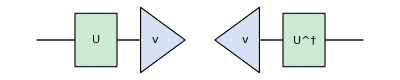

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-4,0}],ket["v"],opU["U",{-2,0}],Line[{#,0}&/@{3,7}],bra["v",{3,0}],opU["U\^†",{5,0}]},ImageSize->{Automatic,30}]]
```

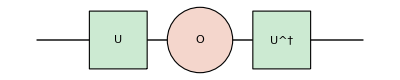

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-4,4}],opH["O"],opU["U",{-2,0}],opU["U\^†",{2,0}]},ImageSize->{Automatic,30}]]
```

The operator Ô is also made of ket and bra states, so the unitary operator must be applied from both sides, when transforming an operator.

The expectation value of an observable is invariant under basis transformation. (Physical reality should be basis-independent.)

⟨O⟩=ψ Ô ψ→ψ(Û)^† Û Ô (Û)^†Û ψ=ψ𝟙 Ô 𝟙ψ=⟨O⟩.

#### Matrix Diagonalization

Diagonalization of a Hermitian operator: find a unitary operator Û to bring the Hermitian operator Ô to diagonal form by transforming to its eigenbasis.

Ô=∑_k O_k O_k O_k,
Û=∑_k kO_k,

such that under Ô→Û Ô (Û)^†,

Λ̂=Û Ô (Û)^†=∑_k k O_k k≏(O_1 |   |  
  | O_2 |  
  |   | ⋱)

is diagonal in the basis of one-hot vectors k.

Every Hermitian matrix can be written as

Ô=(Û)^†Λ̂ Û,

with Λ̂ being diagonal and Û being unitary.

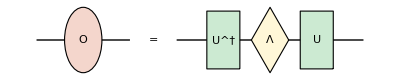

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-2,2}],opH["O"],Line[{#,0}&/@{4,12}],opU["U\^†",{6,0}],opD["Λ",{8,0}],opU["U",{10,0}],Text["=",{3,0}]},ImageSize->{Automatic,30}]]
```

Or equivalently, the unitary transformation Û brings the Hermitian matrix to its diagonal form,

Û Ô (Û)^†=Λ̂.

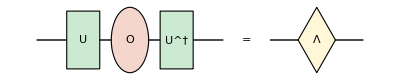

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{Line[{#,0}&/@{-4,4}],opH["O"],opU["U",{-2,0}],opU["U\^†",{2,0}],Line[{#,0}&/@{6,10}],opD["Λ",{8,0}],Text["=",{5,0}]},ImageSize->{Automatic,30}]]
```

Example: diagonalization of Pauli matrix

The Pauli matrix (σ̂)^x can be diagonalized by the following unitary transformation (whose row vectors are bra eigenvectors of (σ̂)^x)

(Û)_H=(+
-)≏1/(√2)(1 | 1
1 | -1).

This unitary operation (Û)_H is also known as the Hadamard gate in quantum information, an example of single-qubit gate.

Under the unitary transformation, (σ̂)^x is brought to its diagonal form, which is (σ̂)^z

(Û)_H (σ̂)^x (Û)_H^†≏1/(√2)(1 | 1
1 | -1)(0 | 1
1 | 0)1/(√2)(1 | 1
1 | -1)
=(1 | 0
0 | -1)≏(σ̂)^z.

#### Hermitian Generators

If Hermitian operators are generalization of real numbers, then unitary operators are generalization of phase factors. (z∈ℂ and |z|=1)

z^*z=z z^*=(|z|)^2=1.

For complex numbers, a phase factor can be written as z=ⅇ^(ⅈ θ), where θ∈ℝ is a real phase angle.

Similar ideas apply to unitary operators: every unitary operator can be generated by a Hermitian operator Θ̂ in the form of

Û=ⅇ^(ⅈ Θ̂).

Given a Hermitian operator Θ̂

Θ̂=∑_k Θ_k(𝒫̂)_(Θ=Θ_k)

by ⅇ^(ⅈ Θ̂) we mean

either by operator Taylor expansion Eq. (DisplayFormulaNumbered)

ⅇ^(ⅈ Θ̂)=𝟙+ⅈ Θ̂+(ⅈ Θ̂)^2/(2!)+(ⅈ Θ̂)^3/(3!)+….

or by spectral decomposition (HW Homework)

ⅇ^(ⅈ Θ̂)=∑_k ⅇ^(ⅈ Θ_k)(𝒫̂)_(Θ=Θ_k)

Don’t do element-wise exponentiation on the matrix!

Use Eq. (DisplayFormulaNumbered) to show that Û=ⅇ^(ⅈ Θ̂) is unitary as long as Θ̂ is Hermitian.

(Û)^†Û=(ⅇ^(ⅈ Θ̂))^†ⅇ^(ⅈ Θ̂)
=(∑_k ⅇ^(ⅈ Θ_k)(𝒫̂)_(Θ=Θ_k))^†(∑_l ⅇ^(ⅈ Θ_l)(𝒫̂)_(Θ=Θ_l))
=∑_(k,l) ⅇ^(-ⅈ Θ_k)ⅇ^(ⅈ Θ_l)(𝒫̂)_(Θ=Θ_k)(𝒫̂)_(Θ=Θ_l)
=∑_(k,l) ⅇ^(-ⅈ Θ_k)ⅇ^(ⅈ Θ_l)(𝒫̂)_(Θ=Θ_k)δ_kl
=∑_k ⅇ^(-ⅈ Θ_k)ⅇ^(ⅈ Θ_k)(𝒫̂)_(Θ=Θ_k)
=∑_k (𝒫̂)_(Θ=Θ_k)
=𝟙.

and similar for Û (Û)^†=𝟙.

Example: unitary generated by Pauli matrix. Recall Û(θ)=e^(ⅈ θ (σ̂)^y) in (Exc Exercise).

Û(θ)=ⅇ^(ⅈ θ (σ̂)^y)≏(cos θ | sin θ
-sin θ | cos θ).

It implements a basis rotation with θ being the rotation angle:

Û(θ)0≏(cos θ | sin θ
-sin θ | cos θ)(1
0)=(cos θ
-sin θ).

Special case: when θ=0, Û(0)=𝟙 ⇒ no rotation is performed.

More generally, let Û(θ) be the unitary operator that implements certain basis rotation by a real angle θ. When θ=Δθ is small, we can Taylor expand

Û(Δθ)=Û(0)+Û'(0)Δθ+…=𝟙+Û'(0)Δθ+…,

where Û'(0) is ∂_θ Û(θ) evaluated at θ=0.

Û'(0) is also an operator (matrix), usually denoted as Û'(0)=ⅈ Ĝ. We call Ĝ the generator of the rotation/unitary operator, because it generates an infinitesimal rotation

Û(Δθ)=𝟙+ⅈ Δθ Ĝ+....

Û(Δθ) is unitary ⇒ Ĝ is Hermitian.

(U(Δθ))^†U(Δθ)
=(𝟙-ⅈ Δθ (Ĝ)^†+...)(𝟙+ⅈ Δθ Ĝ+...)
=𝟙+ⅈ Δθ(Ĝ-(Ĝ)^†)+…=𝟙.

Large rotations can be accumulated from small rotations.

Û(N Δθ)=(Û(Δθ))^N=(𝟙+ⅈ Δθ Ĝ)^N.

As Δθ is small (but N can be large, s.t. θ=N Δθ is finite),

ln Û(N Δθ)=N ln(𝟙+ⅈ Δθ Ĝ)=ⅈ N Δθ Ĝ,

So Û(N Δθ)=ⅇ^(ⅈ N Δθ Ĝ), we obtain the exponential form

Û(θ)=ⅇ^(ⅈ θ Ĝ).

Conclusion: every Hermitian operator Θ̂=θ Ĝ generates a unitary operator ⅇ^(ⅈ Θ̂) by the exponential map.

### Time Evolution

#### Time-Evolution is Unitary

Unitarity: information is never lost!

Basic assumption: quantum information is preserved under quantum dynamics, i.e. two identical and isolated systems

start out in different states ⇒ remains in different states (towards both future and past).

start out in the same state ⇒ follow identical evolution (towards both future and past).

Although measurement seems to be non-deterministic, evolution of quantum state is deterministic: suppose you know the state at one time, then the quantum equation of motion tell you what it will be later.

ψ(t)=Û(t)ψ(0),

ψ(0) is the initial state, and ψ(t) is the state at time t. Û(t) is the time-evolution operator that takes ψ(0) to ψ(t). ☟We will show that Û(t) should be unitary.

Distinct states remain distinct:

ϕ(0)ψ(0)=0⇒ϕ(t)ψ(t)=ϕ(0)(Û(t))^†Û(t)ψ(0)=0.

Identical states remain the identical:

ψ(0)ψ(0)=1⇒ψ(t)ψ(t)=ψ(0)(Û(t))^†Û(t)ψ(0)=1.

Or, the fact that the probability adds up to 1 must be preserved.

Treat ψ(0) and ϕ(0) as members of any orthonormal basis, then Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) implies

i(Û(t))^†Û(t)j=δ_ij⇒(Û(t))^†Û(t)=𝟙.

Therefore, the time-evolution operator Û(t) is unitary.

#### Hamiltonian

Hamiltonian generates time-evolution!

As a unitary operator, the time-evolution operator is also generated by a Hermitian operator, called the Hamiltonian,

Ĥ=ⅈ Û'(0)=ⅈ ∂_t Û(t)|_(t=0).

For small Δt, infinitesimal evolution is given by

Û(Δt)=𝟙-ⅈ Ĥ Δt+...,

therefore the state evolves as

ψ(Δt)=Û(Δt)ψ(0)=ψ(0)-ⅈ Δt Ĥ ψ(0),

meaning that

ⅈ ∂_t ψ(0)=ⅈ (ψ(Δt)-ψ(0))/Δt=Ĥ ψ(0).

There is nothing special about t=0. Eq. (DisplayFormulaNumbered) should hold at any time.

ⅈ∂_t ψ(t)=Ĥ ψ(t).

This is the Schrödinger equation, the equation of motion for the quantum state.

The Hamiltonian Ĥ(t)=ⅈ Û'(t) can be time-dependent in general.

But in many cases, we consider Ĥ to be time-independent, by assuming the time-translation symmetry.

What happens to Planck’s constant?

ℏ=h/(2π)=1.0545718(13)×10^-34 J s.

In quantum mechanics, the observable associated with the Hamiltonian is the energy. To balance the dimensionality across the Schrödinger equation, Planck’s constant is inserted for Eq. (DisplayFormulaNumbered):

ⅈ ℏ∂_t ψ(t)=Ĥ ψ(t).

Why is ℏ so small? Well, the answer has more to do with biology than with physics ⇒ Why we are so big, heavy and slow? A natural choice for quantum mechanics is to set the units such that ℏ=1. It is a common practice in theoretical physics (we will also use this convention sometimes).

#### Schrödinger Equation: State Dynamics

Postulate 4 (Dynamics): The time-evolution of the state of a quantum system is governed by the Hamiltonian of the system, according to the time-dependent Schrödinger equation.

ⅈ ℏ∂_t ψ(t)=Ĥ ψ(t).

If the Hamiltonian Ĥ is time-independent, we can first find its eigenvalues (or eigen energies) and eigenvectors (or energy eigenstates).

Ĥ E_k=E_k E_k.

This is also called the time-independent Schrödinger equation. Without solving a differential equation, we just need to diagonalize a Hermitian matrix in this case.

Each energy eigenstate will evolve in time simply by a rotating overall phase,

E_k(t)=e^(-ⅈ/ℏ E_k t)E_k.

E_k form a complete set of orthonormal basis, called energy eigenbasis.

Verify that Eq. (DisplayFormulaNumbered) is a solution of Eq. (DisplayFormulaNumbered):

Left-hand side:

ⅈ ℏ∂_t E_k(t)=ⅈ ℏ∂_t (e^(-ⅈ/ℏ E_k t)E_k)
=ⅈ ℏ∂_t (e^(-ⅈ/ℏ E_k t))E_k
=E_k e^(-ⅈ/ℏ E_k t)E_k
=E_k E_k(t),

Right-hand side:

Ĥ E_k(t)=e^(-ⅈ/ℏ E_k t)Ĥ E_k
=e^(-ⅈ/ℏ E_k t)E_k E_k
=E_k E_k(t).

So the two sides matches.

Any initial state ψ(0) will evolve in time by first representing the initial state in the energy eigenbasis, and attaching to each energy eigenstate by its rotating overall phase,

ψ(t)=∑_i e^(-ⅈ/ℏ E_i t)E_iE_iψ(0)
=e^(-ⅈ/ℏ Ĥ t)ψ(0).

A time-independent Hamiltonian generates the time-evolution via matrix exponentiation

Û(t)=e^(-ⅈ/ℏ Ĥ t).

However, for time-dependent Hamiltonian, there no such a clean formula. Evolution must be carried out step by step, denoted as a time-ordered exponential

Û(t)=𝒯 exp(-ⅈ/ℏ∫_0^t Ĥ(t')ⅆ t').

##### Larmor Precession and Rabi Oscillation

How to write down a Hamiltonian?

derive it from experiment,

borrow it from some theory we like,

pick one and see what happens.☜

Hamiltonian must be Hermitian anyway. For a single spin (qubit), the most general Hamiltonian takes the form of

Ĥ=h_0 𝟙+h_x(σ̂)^x+h_y(σ̂)^y+h_z(σ̂)^z
=h_0 𝟙+h·σ̂,

where h_0,h_x,h_y,h_z∈ℝ are all real coefficients.

The time-evolution operator (set ℏ=1 in the following)

Û(t)=e^(-ⅈ Ĥ t)
=e^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂),

where |h|=√(h·h) and h̃=h/|h|.

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

Given Ĥ=h_0 𝟙+h·σ̂,

Û(t)=e^(-ⅈ Ĥ t)
=e^(-ⅈ (h_0 𝟙+h·σ̂) t)
=e^(-ⅈ h_0 t)exp(-ⅈ |h|h̃·σ̂ t)
=e^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂).

The last step is by Taylor expansion and using the fact that (h̃·σ̂)^2=𝟙. The problem maps to (HW Homework) by n=h̃ and θ=-|h|t.

A state ψ(0) will evolve with time following

ψ(t)=Û(t)ψ(0)
=e^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂)ψ(0).

If we measure σ on the state ψ(t), the expectation value will be given by

⟨σ⟩_t=ψ(t)σ̂ ψ(t)
=cos(2|h|t)⟨σ⟩_0+sin(2|h|t)h̃×⟨σ⟩_0+(1-cos(2|h|t))h̃(h̃·⟨σ⟩_0).

which also evolves with time.

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).
Hint: Eq. (DisplayFormulaNumbered) can make life much more easier.

Instead of evaluating ⟨σ⟩_t, we first consider m·⟨σ⟩_t

m·⟨σ⟩_t=ψ(t)m·σ̂ψ(t)=ψ(0)(cos(|h|t)𝟙+ⅈ sin(|h|t)h̃·σ̂)m·σ(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂)ψ(0).

The operator inside the bracket reads

(cos(|h|t)𝟙+ⅈ sin(|h|t)h̃·σ̂)m·σ̂(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂)
=cos^2(|h|t)m·σ̂+ⅈ sin(|h|t)cos(|h|t)(h̃·σ̂ m·σ̂-m·σ̂h̃·σ̂)+sin^2(|h|t)h̃·σ̂ m·σ̂h̃·σ̂.

Given a·σ̂ b·σ̂=a·b 𝟙+ⅈ (a×b)·σ̂, we have

h̃·σ̂ m·σ̂=h̃·m 𝟙+ⅈ (h̃×m)·σ̂,
m·σ̂h̃·σ̂=ĥ·m 𝟙-ⅈ (h̃×m)·σ̂,
h̃·σ̂ m·σ̂h̃·σ̂=h̃·m h̃·σ̂+ⅈ (h̃×m)·σ̂h̃·σ̂
=h̃·m h̃·σ̂+ⅈ((h̃×m)·h̃𝟙+ⅈ((h̃×m)×h̃)·σ̂)
=h̃·m h̃·σ̂-((h̃×m)×h̃)·σ̂
=h̃·m h̃·σ̂-(h̃·h̃m·σ̂-h̃·mh̃·σ̂)
=2h̃·m h̃·σ̂-m·σ̂.

Eq. (DisplayFormulaNumbered) becomes

cos^2(|h|t)m·σ̂-2 sin(|h|t)cos(|h|t) (h̃×m)·σ̂+sin^2(|h|t)(2h̃·m h̃·σ̂-m·σ̂)
=cos(2|h|t)m·σ̂+sin(2|h|t)m· (h̃×σ̂)+(1-cos(2|h|t))h̃·m h̃·σ̂.

Plugging back to Eq. (DisplayFormulaNumbered)

m·⟨σ⟩_t=cos(2|h|t)m·⟨σ⟩_0+sin(2|h|t)m· (h̃×⟨σ⟩_0)+(1-cos(2|h|t))h̃·m h̃·⟨σ⟩_0.

Now we take derivatives with respect to m on both sides to get Eq. (DisplayFormulaNumbered).

Larmor precession: assume h=(0,0,h_z) along the z-direction, and parameterize the expectation of the spin vector by ⟨σ⟩=(sin θ cos φ,sin θ sin φ,cos θ).

⟨σ⟩_t=(sin θ_0 cos (φ_0+2 h_z t), sin θ_0 sin(φ_0+2 h_z t),cos θ_0),

where θ_0 and φ_0 are the initial azimuthal and polar angles.

The solution describes the spin ⟨σ⟩ precessing around the axis of the Zeeman field h.

```mathematica
Block[{θ=π/4},Graphics3D[{EdgeForm[None],{Red,Sphere[{0,0,0},0.4],Tube[#{-Sin[θ],0,Cos[θ]}&/@{-1,0.6},0.1],Cone[#{-Sin[θ],0,Cos[θ]}&/@{0.6,1.5},0.2],Text["\!\(⟨σ⟩\)",1.5{-Sin[θ],0,Cos[θ]},{1,-0.5}]},
{Blue,Tube[{0,0,#}&/@{-1.5,1.5},0.05],Cone[{0,0,#}&/@{1.5,2},0.1],Text[Style["\!\(h\)",Bold],{0,0,2},{0,-0.5}]},
{Arrowheads[{0.08,#}&/@{0.25,0.5,0.75}],Dashed,Arrow[Table[1.5{-Sin[θ]Cos[ϕ],-Sin[θ]Sin[ϕ],Cos[θ]},{ϕ,0,2π,π/32}]]}},Lighting->"Neutral",Boxed->False,ImageSize->80]]
```

-Graphics3D-

The precession frequency ω=2|h| is called the Larmor frequency. It can be used to probe the local Zeeman field strength, which has applications in nuclear magnetic resonance (NMR) and nitrogen-vacancy (NV) center.

Energy of a spin in the Zeeman field is ⟨H⟩=-h·⟨σ⟩ (up to some constant energy shift h_0).

Rabi oscillation: a qubit initially prepared in state 0, evolved under the Hamiltonian

Ĥ=Ω (σ̂)^x+Δ (σ̂)^z≏(Δ | Ω
Ω | -Δ),

where Ω is the driving field and Δ is called detuning. The probability to find the qubit in state 1 at time t is given by

(p(1|0))_t=⟨𝒫_1⟩_t=(1-⟨σ^z⟩_t)/2=(sin^2(ω t/2))/(1+(Δ/Ω)^2),

with the Rabi frequency ω=2 √(Ω^2+Δ^2).

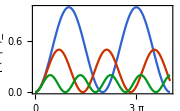
-Graphics--Graphics- | Δ/Ω=0
-Graphics- | Δ/Ω=1
-Graphics- | Δ/Ω=2

```mathematica
Row@{Plot[Evaluate@Table[Sin[Sqrt[1+Δ^2] Ωt/2]^2/(1+Δ^2),{Δ,{0,1,2}}],{Ωt,0,4π},FrameLabel->{"\!\(Ω t\)","\!\(p(1|0)\_t\)"},FrameTicks->{{Automatic,Automatic},{π Range[0,4],None}},GridLines->{π Range[0,4],{0,1}},BaselinePosition->Scaled[0.64],ImageSize->180],
Grid[{Graphics[{#1,Line[{{0,0},{1,0}}]},AspectRatio->0.1,ImageSize->20],Style[StringTemplate["\!\(Δ/Ω=`1`\)"][#2],FontFamily->"CMU"]}&@@@{{Blue,0},{Red,1},{Green,2}},Spacings->{Automatic, 0.1}]}
```

Rabi π-Pulse: flipping 0 to 1 (and vice versa) by a π-pulse (turn on the driving field Ω for time t=π/Ω and turn off) at resonance Δ=0. This implements a NOT gate (or X gate) on a single qubit.

#### Heisenberg Equation: Operator Dynamics

Two pictures of the quantum dynamics:

Schrödinger picture: state evolves in time, operator remains fixed,

⟨O(t)⟩=ψ(t)Ô ψ(t).

Heisenberg picture: operator evolves in time, state remains fixed,

⟨O(t)⟩=ψÔ(t)ψ.

The two pictures are consistent, if

ψ(t)=Û(t)ψ⇒Ô(t)=(Û(t))^†Ô Û(t),

such that Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) are consistent, as they both implies

⟨O(t)⟩=ψ(Û(t))^†Ô Û(t)ψ.

Note: one should only apply one picture at a time, i.e. either the state or the operator is time-dependent, but not both.

In the Heisenberg picture, the time-evolution of an operator

Ô(t)=(Û(t))^†Ô Û(t),

described by the Heisenberg equation

ⅈ ℏ∂_t Ô(t)=[Ô(t),Ĥ].

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

For small Δt (with ℏ=1)

Ô(Δt)=(Û(Δt))^†Ô Û(Δt)
=e^(ⅈ Ĥ Δt)Ô e^(-ⅈ Ĥ Δt)
=(𝟙+ⅈ Ĥ Δt+…)Ô (𝟙-ⅈ Ĥ Δt+…)
=Ô+ⅈ (Ĥ Ô-Ô Ĥ) Δt+…
=Ô-ⅈ [Ô,Ĥ] Δt+…

therefore

ⅈ ∂_t Ô=ⅈ(Ô(Δt)-Ô)/Δt=[Ô,Ĥ].

Restore ℏ, we arrive at Eq. (DisplayFormulaNumbered).

Correspondingly, its expectation value evolves as

ⅈ ℏ∂_t ⟨O(t)⟩=⟨[Ô(t),Ĥ]⟩.

If [Ô,Ĥ]=0, the Heisenberg equation Eq. (DisplayFormulaNumbered) implies that ∂_t ⟨O⟩=0, i.e. O will be invariant in time. The observable O is a conserved quantity (or an integral of motion) if Ô commutes with the Hamiltonian Ĥ.

Consider a single-qubit Hamiltonian H=h·Ŝ, where Ŝ=ℏ/2 σ̂ is the spin operator.
(i) Show that the expectation values of the spin operator evolves as ∂_t ⟨S⟩=h×⟨S⟩.
(ii) Show that
⟨S(t)⟩=cos(|h|t)⟨S(0)⟩+sin(|h|t)h̃×⟨S(0)⟩+(1-cos(|h|t))h̃(h̃·⟨S(0)⟩)
is a solution of ∂_t ⟨S⟩=h×⟨S⟩, where h̃=h/|h|.
This describes the dynamics of a spin in a Zeeman field h.
(iii) Show that the spin component along the Zeeman field h̃·S is a conserved quantity.